```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["MySQL(Connector/J)"];
conn1=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/gestionenegozio"],"Username"->"root","Password"->"root"]
```

JDBC::error: "Communications link failure\n\nThe last packet sent successfully to the server was 0 milliseconds ago. The driver has not received any packets from the server."

$Failed

```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["MySQL(Connector/J)"];
conn1=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/gestionenegozio"],"Username"->"root","Password"->"root"]
```

JDBC::error: "Access denied for user 'root'@'localhost' (using password: YES)"

$Failed

JDBC::error: "Access denied for user 'testtest'@'localhost' (using password: YES)"

$Failed

```mathematica
Needs["DatabaseLink`"];

conn1=OpenSQLConnection[JDBC["MySQL","127.0.0.1:3306/gestionenegozio"],"Username"->"root","Password"->"root"]
```

JDBC::classnotfound: "MySQL"

$Failed

```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["MySQL(Connector/J)"];
conn1=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/classicmodels"],"Username"->"root","Password"->"root"]
```

JDBC::error: "Access denied for user 'root'@'localhost' (using password: YES)"

$Failed

```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["MySQL(Connector/J)"];
conn1=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/classicmodels"],"Username"->"root","Password"->""]
```

```mathematica
SQLConnection[…]
SQLTables[conn1]
```

SQLConnection[…]

{SQLTable[customers,TableType→TABLE],SQLTable[employees,TableType→TABLE],SQLTable[offices,TableType→TABLE],SQLTable[orderdetails,TableType→TABLE],SQLTable[orders,TableType→TABLE],SQLTable[payments,TableType→TABLE],SQLTable[productlines,TableType→TABLE],SQLTable[products,TableType→TABLE]}

```mathematica
conn = OpenSQLConnection[]
```

$Canceled

```mathematica
data=SQLExecute[conn1,"SELECT * FROM customers"];
```

```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["MySQL(Connector/J)"];
conn1=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/classicmodels"],"Username"->"root","Password"->""]
```

SQLExecute::shdw: Symbol "SQLExecute" appears in multiple contexts {"DatabaseLink`", "Global`"}; definitions in context "DatabaseLink`" may shadow or be shadowed by other definitions.

SQLConnection[…]

```mathematica
data=SQLExecute[conn1,"SELECT * FROM customers"];
data
```

{{103,Atelier graphique,Schmitt,Carine ,40.32.2555,54, rue Royale,Null,Nantes,Null,44000,France,1370,21000.},{112,Signal Gift Stores,King,Jean,7025551838,8489 Strong St.,Null,Las Vegas,NV,83030,USA,1166,71800.},{114,Australian Collectors, Co.,Ferguson,Peter,03 9520 4555,636 St Kilda Road,Level 3,Melbourne,Victoria,3004,Australia,1611,117300.},{119,La Rochelle Gifts,Labrune,Janine ,40.67.8555,67, rue des Cinquante Otages,Null,Nantes,Null,44000,France,1370,118200.},{121,Baane Mini Imports,Bergulfsen,Jonas ,07-98 9555,Erling Skakkes gate 78,Null,Stavern,Null,4110,Norway,1504,81700.},{124,Mini Gifts Distributors Ltd.,Nelson,Susan,4155551450,5677 Strong St.,Null,San Rafael,CA,97562,USA,1165,210500.},{125,Havel & Zbyszek Co,Piestrzeniewicz,Zbyszek ,(26) 642-7555,ul. Filtrowa 68,Null,Warszawa,Null,01-012,Poland,Null,0.},{128,Blauer See Auto, Co.,Keitel,Roland,+49 69 66 90 2555,Lyonerstr. 34,Null,Frankfurt,Null,60528,Germany,1504,59700.},{129,Mini Wheels Co.,Murphy,Julie,6505555787,5557 North Pendale Street,Null,San Francisco,CA,94217,USA,1165,64600.},{131,Land of Toys Inc.,Lee,Kwai,2125557818,897 Long Airport Avenue,Null,NYC,NY,10022,USA,1323,114900.},{141,Euro+ Shopping Channel,Freyre,Diego ,(91) 555 94 44,C/ Moralzarzal, 86,Null,Madrid,Null,28034,Spain,1370,227600.},{144,Volvo Model Replicas, Co,Berglund,Christina ,0921-12 3555,Berguvsvägen  8,Null,Luleå,Null,S-958 22,Sweden,1504,53100.},{145,Danish Wholesale Imports,Petersen,Jytte ,31 12 3555,Vinbæltet 34,Null,Kobenhavn,Null,1734,Denmark,1401,83400.},{146,Saveley & Henriot, Co.,Saveley,Mary ,78.32.5555,2, rue du Commerce,Null,Lyon,Null,69004,France,1337,123900.},{148,Dragon Souveniers, Ltd.,Natividad,Eric,+65 221 7555,Bronz Sok.,Bronz Apt. 3/6 Tesvikiye,Singapore,Null,079903,Singapore,1621,103800.},{151,Muscle Machine Inc,Young,Jeff,2125557413,4092 Furth Circle,Suite 400,NYC,NY,10022,USA,1286,138500.},{157,Diecast Classics Inc.,Leong,Kelvin,2155551555,7586 Pompton St.,Null,Allentown,PA,70267,USA,1216,100600.},{161,Technics Stores Inc.,Hashimoto,Juri,6505556809,9408 Furth Circle,Null,Burlingame,CA,94217,USA,1165,84600.},{166,Handji Gifts& Co,Victorino,Wendy,+65 224 1555,106 Linden Road Sandown,2nd Floor,Singapore,Null,069045,Singapore,1612,97900.},{167,Herkku Gifts,Oeztan,Veysel,+47 2267 3215,Brehmen St. 121,PR 334 Sentrum,Bergen,Null,N 5804,Norway  ,1504,96800.},{168,American Souvenirs Inc,Franco,Keith,2035557845,149 Spinnaker Dr.,Suite 101,New Haven,CT,97823,USA,1286,0.},{169,Porto Imports Co.,de Castro,Isabel ,(1) 356-5555,Estrada da saúde n. 58,Null,Lisboa,Null,1756,Portugal,Null,0.},{171,Daedalus Designs Imports,Rancé,Martine ,20.16.1555,184, chaussée de Tournai,Null,Lille,Null,59000,France,1370,82900.},{172,La Corne D'abondance, Co.,Bertrand,Marie,(1) 42.34.2555,265, boulevard Charonne,Null,Paris,Null,75012,France,1337,84300.},{173,Cambridge Collectables Co.,Tseng,Jerry,6175555555,4658 Baden Av.,Null,Cambridge,MA,51247,USA,1188,43400.},{175,Gift Depot Inc.,King,Julie,2035552570,25593 South Bay Ln.,Null,Bridgewater,CT,97562,USA,1323,84300.},{177,Osaka Souveniers Co.,Kentary,Mory,+81 06 6342 5555,1-6-20 Dojima,Null,Kita-ku,Osaka, 530-0003,Japan,1621,81200.},{181,Vitachrome Inc.,Frick,Michael,2125551500,2678 Kingston Rd.,Suite 101,NYC,NY,10022,USA,1286,76400.},{186,Toys of Finland, Co.,Karttunen,Matti,90-224 8555,Keskuskatu 45,Null,Helsinki,Null,21240,Finland,1501,96500.},{187,AV Stores, Co.,Ashworth,Rachel,(171) 555-1555,Fauntleroy Circus,Null,Manchester,Null,EC2 5NT,UK,1501,136800.},{189,Clover Collections, Co.,Cassidy,Dean,+353 1862 1555,25 Maiden Lane,Floor No. 4,Dublin,Null,2,Ireland,1504,69400.},{198,Auto-Moto Classics Inc.,Taylor,Leslie,6175558428,16780 Pompton St.,Null,Brickhaven,MA,58339,USA,1216,23000.},{201,UK Collectables, Ltd.,Devon,Elizabeth,(171) 555-2282,12, Berkeley Gardens Blvd,Null,Liverpool,Null,WX1 6LT,UK,1501,92700.},{202,Canadian Gift Exchange Network,Tamuri,Yoshi ,(604) 555-3392,1900 Oak St.,Null,Vancouver,BC,V3F 2K1,Canada,1323,90300.},{204,Online Mini Collectables,Barajas,Miguel,6175557555,7635 Spinnaker Dr.,Null,Brickhaven,MA,58339,USA,1188,68700.},{205,Toys4GrownUps.com,Young,Julie,6265557265,78934 Hillside Dr.,Null,Pasadena,CA,90003,USA,1166,90700.},{206,Asian Shopping Network, Co,Walker,Brydey,+612 9411 1555,Suntec Tower Three,8 Temasek,Singapore,Null,038988,Singapore,Null,0.},{209,Mini Caravy,Citeaux,Frédérique ,88.60.1555,24, place Kléber,Null,Strasbourg,Null,67000,France,1370,53800.},{211,King Kong Collectables, Co.,Gao,Mike,+852 2251 1555,Bank of China Tower,1 Garden Road,Central Hong Kong,Null,Null,Hong Kong,1621,58600.},{216,Enaco Distributors,Saavedra,Eduardo ,(93) 203 4555,Rambla de Cataluña, 23,Null,Barcelona,Null,08022,Spain,1702,60300.},{219,Boards & Toys Co.,Young,Mary,3105552373,4097 Douglas Av.,Null,Glendale,CA,92561,USA,1166,11000.},{223,Natürlich Autos,Kloss,Horst ,0372-555188,Taucherstraße 10,Null,Cunewalde,Null,01307,Germany,Null,0.},{227,Heintze Collectables,Ibsen,Palle,86 21 3555,Smagsloget 45,Null,Århus,Null,8200,Denmark,1401,120800.},{233,Québec Home Shopping Network,Fresnière,Jean ,(514) 555-8054,43 rue St. Laurent,Null,Montréal,Québec,H1J 1C3,Canada,1286,48700.},{237,ANG Resellers,Camino,Alejandra ,(91) 745 6555,Gran Vía, 1,Null,Madrid,Null,28001,Spain,Null,0.},{239,Collectable Mini Designs Co.,Thompson,Valarie,7605558146,361 Furth Circle,Null,San Diego,CA,91217,USA,1166,105000.},{240,giftsbymail.co.uk,Bennett,Helen ,(198) 555-8888,Garden House,Crowther Way 23,Cowes,Isle of Wight,PO31 7PJ,UK,1501,93900.},{242,Alpha Cognac,Roulet,Annette ,61.77.6555,1 rue Alsace-Lorraine,Null,Toulouse,Null,31000,France,1370,61100.},{247,Messner Shopping Network,Messner,Renate ,069-0555984,Magazinweg 7,Null,Frankfurt,Null,60528,Germany,Null,0.},{249,Amica Models & Co.,Accorti,Paolo ,011-4988555,Via Monte Bianco 34,Null,Torino,Null,10100,Italy,1401,113000.},{250,Lyon Souveniers,Da Silva,Daniel,+33 1 46 62 7555,27 rue du Colonel Pierre Avia,Null,Paris,Null,75508,France,1337,68100.},{256,Auto Associés & Cie.,Tonini,Daniel ,30.59.8555,67, avenue de l'Europe,Null,Versailles,Null,78000,France,1370,77900.},{259,Toms Spezialitäten, Ltd,Pfalzheim,Henriette ,0221-5554327,Mehrheimerstr. 369,Null,Köln,Null,50739,Germany,1504,120400.},{260,Royal Canadian Collectables, Ltd.,Lincoln,Elizabeth ,(604) 555-4555,23 Tsawassen Blvd.,Null,Tsawassen,BC,T2F 8M4,Canada,1323,89600.},{273,Franken Gifts, Co,Franken,Peter ,089-0877555,Berliner Platz 43,Null,München,Null,80805,Germany,Null,0.},{276,Anna's Decorations, Ltd,O'Hara,Anna,02 9936 8555,201 Miller Street,Level 15,North Sydney,NSW,2060,Australia,1611,107800.},{278,Rovelli Gifts,Rovelli,Giovanni ,035-640555,Via Ludovico il Moro 22,Null,Bergamo,Null,24100,Italy,1401,119600.},{282,Souveniers And Things Co.,Huxley,Adrian,+61 2 9495 8555,Monitor Money Building,815 Pacific Hwy,Chatswood,NSW,2067,Australia,1611,93300.},{286,Marta's Replicas Co.,Hernandez,Marta,6175558555,39323 Spinnaker Dr.,Null,Cambridge,MA,51247,USA,1216,123700.},{293,BG&E Collectables,Harrison,Ed,+41 26 425 50 01,Rte des Arsenaux 41 ,Null,Fribourg,Null,1700,Switzerland,Null,0.},{298,Vida Sport, Ltd,Holz,Mihael,0897-034555,Grenzacherweg 237,Null,Genève,Null,1203,Switzerland,1702,141300.},{299,Norway Gifts By Mail, Co.,Klaeboe,Jan,+47 2212 1555,Drammensveien 126A,PB 211 Sentrum,Oslo,Null,N 0106,Norway  ,1504,95100.},{303,Schuyler Imports,Schuyler,Bradley,+31 20 491 9555,Kingsfordweg 151,Null,Amsterdam,Null,1043 GR,Netherlands,Null,0.},{307,Der Hund Imports,Andersen,Mel,030-0074555,Obere Str. 57,Null,Berlin,Null,12209,Germany,Null,0.},{311,Oulu Toy Supplies, Inc.,Koskitalo,Pirkko,981-443655,Torikatu 38,Null,Oulu,Null,90110,Finland,1501,90500.},{314,Petit Auto,Dewey,Catherine ,(02) 5554 67,Rue Joseph-Bens 532,Null,Bruxelles,Null,B-1180,Belgium,1401,79900.},{319,Mini Classics,Frick,Steve,9145554562,3758 North Pendale Street,Null,White Plains,NY,24067,USA,1323,102700.},{320,Mini Creations Ltd.,Huang,Wing,5085559555,4575 Hillside Dr.,Null,New Bedford,MA,50553,USA,1188,94500.},{321,Corporate Gift Ideas Co.,Brown,Julie,6505551386,7734 Strong St.,Null,San Francisco,CA,94217,USA,1165,105000.},{323,Down Under Souveniers, Inc,Graham,Mike,+64 9 312 5555,162-164 Grafton Road,Level 2,Auckland  ,Null,Null,New Zealand,1612,88000.},{324,Stylish Desk Decors, Co.,Brown,Ann ,(171) 555-0297,35 King George,Null,London,Null,WX3 6FW,UK,1501,77000.},{328,Tekni Collectables Inc.,Brown,William,2015559350,7476 Moss Rd.,Null,Newark,NJ,94019,USA,1323,43000.},{333,Australian Gift Network, Co,Calaghan,Ben,61-7-3844-6555,31 Duncan St. West End,Null,South Brisbane,Queensland,4101,Australia,1611,51600.},{334,Suominen Souveniers,Suominen,Kalle,+358 9 8045 555,Software Engineering Center,SEC Oy,Espoo,Null,FIN-02271,Finland,1501,98800.},{335,Cramer Spezialitäten, Ltd,Cramer,Philip ,0555-09555,Maubelstr. 90,Null,Brandenburg,Null,14776,Germany,Null,0.},{339,Classic Gift Ideas, Inc,Cervantes,Francisca,2155554695,782 First Street,Null,Philadelphia,PA,71270,USA,1188,81100.},{344,CAF Imports,Fernandez,Jesus,+34 913 728 555,Merchants House,27-30 Merchant's Quay,Madrid,Null,28023,Spain,1702,59600.},{347,Men 'R' US Retailers, Ltd.,Chandler,Brian,2155554369,6047 Douglas Av.,Null,Los Angeles,CA,91003,USA,1166,57700.},{348,Asian Treasures, Inc.,McKenna,Patricia ,2967 555,8 Johnstown Road,Null,Cork,Co. Cork,Null,Ireland,Null,0.},{350,Marseille Mini Autos,Lebihan,Laurence ,91.24.4555,12, rue des Bouchers,Null,Marseille,Null,13008,France,1337,65000.},{353,Reims Collectables,Henriot,Paul ,26.47.1555,59 rue de l'Abbaye,Null,Reims,Null,51100,France,1337,81100.},{356,SAR Distributors, Co,Kuger,Armand,+27 21 550 3555,1250 Pretorius Street,Null,Hatfield,Pretoria,0028,South Africa,Null,0.},{357,GiftsForHim.com,MacKinlay,Wales,64-9-3763555,199 Great North Road,Null,Auckland,Null,Null,New Zealand,1612,77700.},{361,Kommission Auto,Josephs,Karin,0251-555259,Luisenstr. 48,Null,Münster,Null,44087,Germany,Null,0.},{362,Gifts4AllAges.com,Yoshido,Juri,6175559555,8616 Spinnaker Dr.,Null,Boston,MA,51003,USA,1216,41900.},{363,Online Diecast Creations Co.,Young,Dorothy,6035558647,2304 Long Airport Avenue,Null,Nashua,NH,62005,USA,1216,114200.},{369,Lisboa Souveniers, Inc,Rodriguez,Lino ,(1) 354-2555,Jardim das rosas n. 32,Null,Lisboa,Null,1675,Portugal,Null,0.},{376,Precious Collectables,Urs,Braun,0452-076555,Hauptstr. 29,Null,Bern,Null,3012,Switzerland,1702,0.},{379,Collectables For Less Inc.,Nelson,Allen,6175558555,7825 Douglas Av.,Null,Brickhaven,MA,58339,USA,1188,70700.},{381,Royale Belge,Cartrain,Pascale ,(071) 23 67 2555,Boulevard Tirou, 255,Null,Charleroi,Null,B-6000,Belgium,1401,23500.},{382,Salzburg Collectables,Pipps,Georg ,6562-9555,Geislweg 14,Null,Salzburg,Null,5020,Austria,1401,71700.},{385,Cruz & Sons Co.,Cruz,Arnold,+63 2 555 3587,15 McCallum Street,NatWest Center #13-03,Makati City,Null,1227 MM,Philippines,1621,81500.},{386,L'ordine Souveniers,Moroni,Maurizio ,0522-556555,Strada Provinciale 124,Null,Reggio Emilia,Null,42100,Italy,1401,121400.},{398,Tokyo Collectables, Ltd,Shimamura,Akiko,+81 3 3584 0555,2-2-8 Roppongi,Null,Minato-ku,Tokyo,106-0032,Japan,1621,94400.},{406,Auto Canal+ Petit,Perrier,Dominique,(1) 47.55.6555,25, rue Lauriston,Null,Paris,Null,75016,France,1337,95000.},{409,Stuttgart Collectable Exchange,Müller,Rita ,0711-555361,Adenauerallee 900,Null,Stuttgart,Null,70563,Germany,Null,0.},{412,Extreme Desk Decorations, Ltd,McRoy,Sarah,04 499 9555,101 Lambton Quay,Level 11,Wellington,Null,Null,New Zealand,1612,86800.},{415,Bavarian Collectables Imports, Co.,Donnermeyer,Michael, +49 89 61 08 9555,Hansastr. 15,Null,Munich,Null,80686,Germany,1504,77000.},{424,Classic Legends Inc.,Hernandez,Maria,2125558493,5905 Pompton St.,Suite 750,NYC,NY,10022,USA,1286,67500.},{443,Feuer Online Stores, Inc,Feuer,Alexander ,0342-555176,Heerstr. 22,Null,Leipzig,Null,04179,Germany,Null,0.},{447,Gift Ideas Corp.,Lewis,Dan,2035554407,2440 Pompton St.,Null,Glendale,CT,97561,USA,1323,49700.},{448,Scandinavian Gift Ideas,Larsson,Martha,0695-34 6555,Åkergatan 24,Null,Bräcke,Null,S-844 67,Sweden,1504,116400.},{450,The Sharp Gifts Warehouse,Frick,Sue,4085553659,3086 Ingle Ln.,Null,San Jose,CA,94217,USA,1165,77600.},{452,Mini Auto Werke,Mendel,Roland ,7675-3555,Kirchgasse 6,Null,Graz,Null,8010,Austria,1401,45300.},{455,Super Scale Inc.,Murphy,Leslie,2035559545,567 North Pendale Street,Null,New Haven,CT,97823,USA,1286,95400.},{456,Microscale Inc.,Choi,Yu,2125551957,5290 North Pendale Street,Suite 200,NYC,NY,10022,USA,1286,39800.},{458,Corrida Auto Replicas, Ltd,Sommer,Martín ,(91) 555 22 82,C/ Araquil, 67,Null,Madrid,Null,28023,Spain,1702,104600.},{459,Warburg Exchange,Ottlieb,Sven ,0241-039123,Walserweg 21,Null,Aachen,Null,52066,Germany,Null,0.},{462,FunGiftIdeas.com,Benitez,Violeta,5085552555,1785 First Street,Null,New Bedford,MA,50553,USA,1216,85800.},{465,Anton Designs, Ltd.,Anton,Carmen,+34 913 728555,c/ Gobelas, 19-1 Urb. La Florida,Null,Madrid,Null,28023,Spain,Null,0.},{471,Australian Collectables, Ltd,Clenahan,Sean,61-9-3844-6555,7 Allen Street,Null,Glen Waverly,Victoria,3150,Australia,1611,60300.},{473,Frau da Collezione,Ricotti,Franco,+39 022515555,20093 Cologno Monzese,Alessandro Volta 16,Milan,Null,Null,Italy,1401,34800.},{475,West Coast Collectables Co.,Thompson,Steve,3105553722,3675 Furth Circle,Null,Burbank,CA,94019,USA,1166,55400.},{477,Mit Vergnügen & Co.,Moos,Hanna ,0621-08555,Forsterstr. 57,Null,Mannheim,Null,68306,Germany,Null,0.},{480,Kremlin Collectables, Co.,Semenov,Alexander ,+7 812 293 0521,2 Pobedy Square,Null,Saint Petersburg,Null,196143,Russia,Null,0.},{481,Raanan Stores, Inc,Altagar,G M,Raanan,+ 972 9 959 8555,3 Hagalim Blv.,Null,Herzlia,Null,47625,Israel,Null,0.},{484,Iberia Gift Imports, Corp.,Roel,José Pedro ,(95) 555 82 82,C/ Romero, 33,Null,Sevilla,Null,41101,Spain,1702,65700.},{486,Motor Mint Distributors Inc.,Salazar,Rosa,2155559857,11328 Douglas Av.,Null,Philadelphia,PA,71270,USA,1323,72600.},{487,Signal Collectibles Ltd.,Taylor,Sue,4155554312,2793 Furth Circle,Null,Brisbane,CA,94217,USA,1165,60300.},{489,Double Decker Gift Stores, Ltd,Smith,Thomas ,(171) 555-7555,120 Hanover Sq.,Null,London,Null,WA1 1DP,UK,1501,43300.},{495,Diecast Collectables,Franco,Valarie,6175552555,6251 Ingle Ln.,Null,Boston,MA,51003,USA,1188,85100.},{496,Kelly's Gift Shop,Snowden,Tony,+64 9 5555500,Arenales 1938 3'A',Null,Auckland  ,Null,Null,New Zealand,1612,110000.}}

```mathematica
data=SQLExecute[conn1,"INSERT INTO customers (customerNumber, customerName, contactLastName, contactFirstName, phone, addressLine1, city, country) VALUES ('123456', 'Lorenzo Lanzarone', 'Lanzarone', 'Lorenzo', '3318672565', 'Via Santo Stefano', 'Funo di Argelato', 'Italia'); "];
```

```mathematica
1
```

1

```mathematica
data
```

1

```mathematica
data=SQLExecute[conn1,"SELECT * FROM customers"];
```

```mathematica
Transpose[%63]
```

{{103,112,114,119,121,124,125,128,129,131,141,144,145,146,148,151,157,161,166,167,168,169,171,172,173,175,177,181,186,187,189,198,201,202,204,205,206,209,211,216,219,223,227,233,237,239,240,242,247,249,250,256,259,260,273,276,278,282,286,293,298,299,303,307,311,314,319,320,321,323,324,328,333,334,335,339,344,347,348,350,353,356,357,361,362,363,369,376,379,381,382,385,386,398,406,409,412,415,424,443,447,448,450,452,455,456,458,459,462,465,471,473,475,477,480,481,484,486,487,489,495,496,123456},{Atelier graphique,Signal Gift Stores,Australian Collectors, Co.,La Rochelle Gifts,Baane Mini Imports,Mini Gifts Distributors Ltd.,Havel & Zbyszek Co,Blauer See Auto, Co.,Mini Wheels Co.,Land of Toys Inc.,Euro+ Shopping Channel,Volvo Model Replicas, Co,Danish Wholesale Imports,Saveley & Henriot, Co.,Dragon Souveniers, Ltd.,Muscle Machine Inc,Diecast Classics Inc.,Technics Stores Inc.,Handji Gifts& Co,Herkku Gifts,American Souvenirs Inc,Porto Imports Co.,Daedalus Designs Imports,La Corne D'abondance, Co.,Cambridge Collectables Co.,Gift Depot Inc.,Osaka Souveniers Co.,Vitachrome Inc.,Toys of Finland, Co.,AV Stores, Co.,Clover Collections, Co.,Auto-Moto Classics Inc.,UK Collectables, Ltd.,Canadian Gift Exchange Network,Online Mini Collectables,Toys4GrownUps.com,Asian Shopping Network, Co,Mini Caravy,King Kong Collectables, Co.,Enaco Distributors,Boards & Toys Co.,Natürlich Autos,Heintze Collectables,Québec Home Shopping Network,ANG Resellers,Collectable Mini Designs Co.,giftsbymail.co.uk,Alpha Cognac,Messner Shopping Network,Amica Models & Co.,Lyon Souveniers,Auto Associés & Cie.,Toms Spezialitäten, Ltd,Royal Canadian Collectables, Ltd.,Franken Gifts, Co,Anna's Decorations, Ltd,Rovelli Gifts,Souveniers And Things Co.,Marta's Replicas Co.,BG&E Collectables,Vida Sport, Ltd,Norway Gifts By Mail, Co.,Schuyler Imports,Der Hund Imports,Oulu Toy Supplies, Inc.,Petit Auto,Mini Classics,Mini Creations Ltd.,Corporate Gift Ideas Co.,Down Under Souveniers, Inc,Stylish Desk Decors, Co.,Tekni Collectables Inc.,Australian Gift Network, Co,Suominen Souveniers,Cramer Spezialitäten, Ltd,Classic Gift Ideas, Inc,CAF Imports,Men 'R' US Retailers, Ltd.,Asian Treasures, Inc.,Marseille Mini Autos,Reims Collectables,SAR Distributors, Co,GiftsForHim.com,Kommission Auto,Gifts4AllAges.com,Online Diecast Creations Co.,Lisboa Souveniers, Inc,Precious Collectables,Collectables For Less Inc.,Royale Belge,Salzburg Collectables,Cruz & Sons Co.,L'ordine Souveniers,Tokyo Collectables, Ltd,Auto Canal+ Petit,Stuttgart Collectable Exchange,Extreme Desk Decorations, Ltd,Bavarian Collectables Imports, Co.,Classic Legends Inc.,Feuer Online Stores, Inc,Gift Ideas Corp.,Scandinavian Gift Ideas,The Sharp Gifts Warehouse,Mini Auto Werke,Super Scale Inc.,Microscale Inc.,Corrida Auto Replicas, Ltd,Warburg Exchange,FunGiftIdeas.com,Anton Designs, Ltd.,Australian Collectables, Ltd,Frau da Collezione,West Coast Collectables Co.,Mit Vergnügen & Co.,Kremlin Collectables, Co.,Raanan Stores, Inc,Iberia Gift Imports, Corp.,Motor Mint Distributors Inc.,Signal Collectibles Ltd.,Double Decker Gift Stores, Ltd,Diecast Collectables,Kelly's Gift Shop,Lorenzo Lanzarone},{Schmitt,King,Ferguson,Labrune,Bergulfsen,Nelson,Piestrzeniewicz,Keitel,Murphy,Lee,Freyre,Berglund,Petersen,Saveley,Natividad,Young,Leong,Hashimoto,Victorino,Oeztan,Franco,de Castro,Rancé,Bertrand,Tseng,King,Kentary,Frick,Karttunen,Ashworth,Cassidy,Taylor,Devon,Tamuri,Barajas,Young,Walker,Citeaux,Gao,Saavedra,Young,Kloss,Ibsen,Fresnière,Camino,Thompson,Bennett,Roulet,Messner,Accorti,Da Silva,Tonini,Pfalzheim,Lincoln,Franken,O'Hara,Rovelli,Huxley,Hernandez,Harrison,Holz,Klaeboe,Schuyler,Andersen,Koskitalo,Dewey,Frick,Huang,Brown,Graham,Brown,Brown,Calaghan,Suominen,Cramer,Cervantes,Fernandez,Chandler,McKenna,Lebihan,Henriot,Kuger,MacKinlay,Josephs,Yoshido,Young,Rodriguez,Urs,Nelson,Cartrain,Pipps,Cruz,Moroni,Shimamura,Perrier,Müller,McRoy,Donnermeyer,Hernandez,Feuer,Lewis,Larsson,Frick,Mendel,Murphy,Choi,Sommer,Ottlieb,Benitez,Anton,Clenahan,Ricotti,Thompson,Moos,Semenov,Altagar,G M,Roel,Salazar,Taylor,Smith,Franco,Snowden,Lanzarone},{Carine ,Jean,Peter,Janine ,Jonas ,Susan,Zbyszek ,Roland,Julie,Kwai,Diego ,Christina ,Jytte ,Mary ,Eric,Jeff,Kelvin,Juri,Wendy,Veysel,Keith,Isabel ,Martine ,Marie,Jerry,Julie,Mory,Michael,Matti,Rachel,Dean,Leslie,Elizabeth,Yoshi ,Miguel,Julie,Brydey,Frédérique ,Mike,Eduardo ,Mary,Horst ,Palle,Jean ,Alejandra ,Valarie,Helen ,Annette ,Renate ,Paolo ,Daniel,Daniel ,Henriette ,Elizabeth ,Peter ,Anna,Giovanni ,Adrian,Marta,Ed,Mihael,Jan,Bradley,Mel,Pirkko,Catherine ,Steve,Wing,Julie,Mike,Ann ,William,Ben,Kalle,Philip ,Francisca,Jesus,Brian,Patricia ,Laurence ,Paul ,Armand,Wales,Karin,Juri,Dorothy,Lino ,Braun,Allen,Pascale ,Georg ,Arnold,Maurizio ,Akiko,Dominique,Rita ,Sarah,Michael,Maria,Alexander ,Dan,Martha,Sue,Roland ,Leslie,Yu,Martín ,Sven ,Violeta,Carmen,Sean,Franco,Steve,Hanna ,Alexander ,Raanan,José Pedro ,Rosa,Sue,Thomas ,Valarie,Tony,Lorenzo},{40.32.2555,7025551838,03 9520 4555,40.67.8555,07-98 9555,4155551450,(26) 642-7555,+49 69 66 90 2555,6505555787,2125557818,(91) 555 94 44,0921-12 3555,31 12 3555,78.32.5555,+65 221 7555,2125557413,2155551555,6505556809,+65 224 1555,+47 2267 3215,2035557845,(1) 356-5555,20.16.1555,(1) 42.34.2555,6175555555,2035552570,+81 06 6342 5555,2125551500,90-224 8555,(171) 555-1555,+353 1862 1555,6175558428,(171) 555-2282,(604) 555-3392,6175557555,6265557265,+612 9411 1555,88.60.1555,+852 2251 1555,(93) 203 4555,3105552373,0372-555188,86 21 3555,(514) 555-8054,(91) 745 6555,7605558146,(198) 555-8888,61.77.6555,069-0555984,011-4988555,+33 1 46 62 7555,30.59.8555,0221-5554327,(604) 555-4555,089-0877555,02 9936 8555,035-640555,+61 2 9495 8555,6175558555,+41 26 425 50 01,0897-034555,+47 2212 1555,+31 20 491 9555,030-0074555,981-443655,(02) 5554 67,9145554562,5085559555,6505551386,+64 9 312 5555,(171) 555-0297,2015559350,61-7-3844-6555,+358 9 8045 555,0555-09555,2155554695,+34 913 728 555,2155554369,2967 555,91.24.4555,26.47.1555,+27 21 550 3555,64-9-3763555,0251-555259,6175559555,6035558647,(1) 354-2555,0452-076555,6175558555,(071) 23 67 2555,6562-9555,+63 2 555 3587,0522-556555,+81 3 3584 0555,(1) 47.55.6555,0711-555361,04 499 9555, +49 89 61 08 9555,2125558493,0342-555176,2035554407,0695-34 6555,4085553659,7675-3555,2035559545,2125551957,(91) 555 22 82,0241-039123,5085552555,+34 913 728555,61-9-3844-6555,+39 022515555,3105553722,0621-08555,+7 812 293 0521,+ 972 9 959 8555,(95) 555 82 82,2155559857,4155554312,(171) 555-7555,6175552555,+64 9 5555500,3318672565},{54, rue Royale,8489 Strong St.,636 St Kilda Road,67, rue des Cinquante Otages,Erling Skakkes gate 78,5677 Strong St.,ul. Filtrowa 68,Lyonerstr. 34,5557 North Pendale Street,897 Long Airport Avenue,C/ Moralzarzal, 86,Berguvsvägen  8,Vinbæltet 34,2, rue du Commerce,Bronz Sok.,4092 Furth Circle,7586 Pompton St.,9408 Furth Circle,106 Linden Road Sandown,Brehmen St. 121,149 Spinnaker Dr.,Estrada da saúde n. 58,184, chaussée de Tournai,265, boulevard Charonne,4658 Baden Av.,25593 South Bay Ln.,1-6-20 Dojima,2678 Kingston Rd.,Keskuskatu 45,Fauntleroy Circus,25 Maiden Lane,16780 Pompton St.,12, Berkeley Gardens Blvd,1900 Oak St.,7635 Spinnaker Dr.,78934 Hillside Dr.,Suntec Tower Three,24, place Kléber,Bank of China Tower,Rambla de Cataluña, 23,4097 Douglas Av.,Taucherstraße 10,Smagsloget 45,43 rue St. Laurent,Gran Vía, 1,361 Furth Circle,Garden House,1 rue Alsace-Lorraine,Magazinweg 7,Via Monte Bianco 34,27 rue du Colonel Pierre Avia,67, avenue de l'Europe,Mehrheimerstr. 369,23 Tsawassen Blvd.,Berliner Platz 43,201 Miller Street,Via Ludovico il Moro 22,Monitor Money Building,39323 Spinnaker Dr.,Rte des Arsenaux 41 ,Grenzacherweg 237,Drammensveien 126A,Kingsfordweg 151,Obere Str. 57,Torikatu 38,Rue Joseph-Bens 532,3758 North Pendale Street,4575 Hillside Dr.,7734 Strong St.,162-164 Grafton Road,35 King George,7476 Moss Rd.,31 Duncan St. West End,Software Engineering Center,Maubelstr. 90,782 First Street,Merchants House,6047 Douglas Av.,8 Johnstown Road,12, rue des Bouchers,59 rue de l'Abbaye,1250 Pretorius Street,199 Great North Road,Luisenstr. 48,8616 Spinnaker Dr.,2304 Long Airport Avenue,Jardim das rosas n. 32,Hauptstr. 29,7825 Douglas Av.,Boulevard Tirou, 255,Geislweg 14,15 McCallum Street,Strada Provinciale 124,2-2-8 Roppongi,25, rue Lauriston,Adenauerallee 900,101 Lambton Quay,Hansastr. 15,5905 Pompton St.,Heerstr. 22,2440 Pompton St.,Åkergatan 24,3086 Ingle Ln.,Kirchgasse 6,567 North Pendale Street,5290 North Pendale Street,C/ Araquil, 67,Walserweg 21,1785 First Street,c/ Gobelas, 19-1 Urb. La Florida,7 Allen Street,20093 Cologno Monzese,3675 Furth Circle,Forsterstr. 57,2 Pobedy Square,3 Hagalim Blv.,C/ Romero, 33,11328 Douglas Av.,2793 Furth Circle,120 Hanover Sq.,6251 Ingle Ln.,Arenales 1938 3'A',Via Santo Stefano},{Null,Null,Level 3,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Bronz Apt. 3/6 Tesvikiye,Suite 400,Null,Null,2nd Floor,PR 334 Sentrum,Suite 101,Null,Null,Null,Null,Null,Null,Suite 101,Null,Null,Floor No. 4,Null,Null,Null,Null,Null,8 Temasek,Null,1 Garden Road,Null,Null,Null,Null,Null,Null,Null,Crowther Way 23,Null,Null,Null,Null,Null,Null,Null,Null,Level 15,Null,815 Pacific Hwy,Null,Null,Null,PB 211 Sentrum,Null,Null,Null,Null,Null,Null,Null,Level 2,Null,Null,Null,SEC Oy,Null,Null,27-30 Merchant's Quay,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,NatWest Center #13-03,Null,Null,Null,Null,Level 11,Null,Suite 750,Null,Null,Null,Null,Null,Null,Suite 200,Null,Null,Null,Null,Null,Alessandro Volta 16,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Nantes,Las Vegas,Melbourne,Nantes,Stavern,San Rafael,Warszawa,Frankfurt,San Francisco,NYC,Madrid,Luleå,Kobenhavn,Lyon,Singapore,NYC,Allentown,Burlingame,Singapore,Bergen,New Haven,Lisboa,Lille,Paris,Cambridge,Bridgewater,Kita-ku,NYC,Helsinki,Manchester,Dublin,Brickhaven,Liverpool,Vancouver,Brickhaven,Pasadena,Singapore,Strasbourg,Central Hong Kong,Barcelona,Glendale,Cunewalde,Århus,Montréal,Madrid,San Diego,Cowes,Toulouse,Frankfurt,Torino,Paris,Versailles,Köln,Tsawassen,München,North Sydney,Bergamo,Chatswood,Cambridge,Fribourg,Genève,Oslo,Amsterdam,Berlin,Oulu,Bruxelles,White Plains,New Bedford,San Francisco,Auckland  ,London,Newark,South Brisbane,Espoo,Brandenburg,Philadelphia,Madrid,Los Angeles,Cork,Marseille,Reims,Hatfield,Auckland,Münster,Boston,Nashua,Lisboa,Bern,Brickhaven,Charleroi,Salzburg,Makati City,Reggio Emilia,Minato-ku,Paris,Stuttgart,Wellington,Munich,NYC,Leipzig,Glendale,Bräcke,San Jose,Graz,New Haven,NYC,Madrid,Aachen,New Bedford,Madrid,Glen Waverly,Milan,Burbank,Mannheim,Saint Petersburg,Herzlia,Sevilla,Philadelphia,Brisbane,London,Boston,Auckland  ,Funo di Argelato},{Null,NV,Victoria,Null,Null,CA,Null,Null,CA,NY,Null,Null,Null,Null,Null,NY,PA,CA,Null,Null,CT,Null,Null,Null,MA,CT,Osaka,NY,Null,Null,Null,MA,Null,BC,MA,CA,Null,Null,Null,Null,CA,Null,Null,Québec,Null,CA,Isle of Wight,Null,Null,Null,Null,Null,Null,BC,Null,NSW,Null,NSW,MA,Null,Null,Null,Null,Null,Null,Null,NY,MA,CA,Null,Null,NJ,Queensland,Null,Null,PA,Null,CA,Co. Cork,Null,Null,Pretoria,Null,Null,MA,NH,Null,Null,MA,Null,Null,Null,Null,Tokyo,Null,Null,Null,Null,NY,Null,CT,Null,CA,Null,CT,NY,Null,Null,MA,Null,Victoria,Null,CA,Null,Null,Null,Null,PA,CA,Null,MA,Null,Null},{44000,83030,3004,44000,4110,97562,01-012,60528,94217,10022,28034,S-958 22,1734,69004,079903,10022,70267,94217,069045,N 5804,97823,1756,59000,75012,51247,97562, 530-0003,10022,21240,EC2 5NT,2,58339,WX1 6LT,V3F 2K1,58339,90003,038988,67000,Null,08022,92561,01307,8200,H1J 1C3,28001,91217,PO31 7PJ,31000,60528,10100,75508,78000,50739,T2F 8M4,80805,2060,24100,2067,51247,1700,1203,N 0106,1043 GR,12209,90110,B-1180,24067,50553,94217,Null,WX3 6FW,94019,4101,FIN-02271,14776,71270,28023,91003,Null,13008,51100,0028,Null,44087,51003,62005,1675,3012,58339,B-6000,5020,1227 MM,42100,106-0032,75016,70563,Null,80686,10022,04179,97561,S-844 67,94217,8010,97823,10022,28023,52066,50553,28023,3150,Null,94019,68306,196143,47625,41101,71270,94217,WA1 1DP,51003,Null,Null},{France,USA,Australia,France,Norway,USA,Poland,Germany,USA,USA,Spain,Sweden,Denmark,France,Singapore,USA,USA,USA,Singapore,Norway  ,USA,Portugal,France,France,USA,USA,Japan,USA,Finland,UK,Ireland,USA,UK,Canada,USA,USA,Singapore,France,Hong Kong,Spain,USA,Germany,Denmark,Canada,Spain,USA,UK,France,Germany,Italy,France,France,Germany,Canada,Germany,Australia,Italy,Australia,USA,Switzerland,Switzerland,Norway  ,Netherlands,Germany,Finland,Belgium,USA,USA,USA,New Zealand,UK,USA,Australia,Finland,Germany,USA,Spain,USA,Ireland,France,France,South Africa,New Zealand,Germany,USA,USA,Portugal,Switzerland,USA,Belgium,Austria,Philippines,Italy,Japan,France,Germany,New Zealand,Germany,USA,Germany,USA,Sweden,USA,Austria,USA,USA,Spain,Germany,USA,Spain,Australia,Italy,USA,Germany,Russia,Israel,Spain,USA,USA,UK,USA,New Zealand,Italia},{1370,1166,1611,1370,1504,1165,Null,1504,1165,1323,1370,1504,1401,1337,1621,1286,1216,1165,1612,1504,1286,Null,1370,1337,1188,1323,1621,1286,1501,1501,1504,1216,1501,1323,1188,1166,Null,1370,1621,1702,1166,Null,1401,1286,Null,1166,1501,1370,Null,1401,1337,1370,1504,1323,Null,1611,1401,1611,1216,Null,1702,1504,Null,Null,1501,1401,1323,1188,1165,1612,1501,1323,1611,1501,Null,1188,1702,1166,Null,1337,1337,Null,1612,Null,1216,1216,Null,1702,1188,1401,1401,1621,1401,1621,1337,Null,1612,1504,1286,Null,1323,1504,1165,1401,1286,1286,1702,Null,1216,Null,1611,1401,1166,Null,Null,Null,1702,1323,1165,1501,1188,1612,Null},{21000.,71800.,117300.,118200.,81700.,210500.,0.,59700.,64600.,114900.,227600.,53100.,83400.,123900.,103800.,138500.,100600.,84600.,97900.,96800.,0.,0.,82900.,84300.,43400.,84300.,81200.,76400.,96500.,136800.,69400.,23000.,92700.,90300.,68700.,90700.,0.,53800.,58600.,60300.,11000.,0.,120800.,48700.,0.,105000.,93900.,61100.,0.,113000.,68100.,77900.,120400.,89600.,0.,107800.,119600.,93300.,123700.,0.,141300.,95100.,0.,0.,90500.,79900.,102700.,94500.,105000.,88000.,77000.,43000.,51600.,98800.,0.,81100.,59600.,57700.,0.,65000.,81100.,0.,77700.,0.,41900.,114200.,0.,0.,70700.,23500.,71700.,81500.,121400.,94400.,95000.,0.,86800.,77000.,67500.,0.,49700.,116400.,77600.,45300.,95400.,39800.,104600.,0.,85800.,0.,60300.,34800.,55400.,0.,0.,0.,65700.,72600.,60300.,43300.,85100.,110000.,Null}}

```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["MySQL(Connector/J)"];
conn1=OpenSQLConnection[JDBC["MySQL(Connector/J)","127.0.0.1:3306/designazioni"],"Username"->"root","Password"->""]
```

SQLConnection[…]

```mathematica
data=SQLExecute[conn1,"SELECT * FROM tesserato"];
data
```

{{1,061537,Andolfo,Angelo,Arbitro regionale giovanile,Regionale - 6a cat.,SQLDateTime[{2019,4,3}],POGGIO RENATICO,FERRARA,EMILIA-ROMAGNA,SQLDateTime[{2002,8,7}],ESTERO,3703279389,bruzzoandolfo@libero.it,2,Poggio Renatico,Null,True,Null,Null,True},357,{427,067896,De Cesare,Lorenzo,Arbitro regionale giovanile,Regionale - 6a cat.,SQLDateTime[{2020,1,15}],Ferrara,FERRARA,EMILIA-ROMAGNA,SQLDateTime[{2006,1,22}],FERRARA,3207277090,lorilego22@gmail.com,2,Ferrara,,True,True,False,False}}
 |  |  |  |

```mathematica
TableForm[%7]
```

1 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 2 | Poggio Renatico | Null | True | Null | Null | True
2 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 2 | Ferrara | NO partite tardi | True | False | False | False
3 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 2 | Ferrara |  | False | False | False | True
4 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 2 | Cento | Null | True | Null | Null | Null
5 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 2 | Ferrara | Null | True | Null | Null | Null
6 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
7 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
8 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 2 | Santa M. M. |  | True | False | False | False
9 | 065109 | Bottura | Giorgio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 2 | Ferrara | Null | True | Null | Null | Null
10 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,23}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 2 | Cento | Null | True | Null | Null | Null
11 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 2 | Ferrara | Null | False | Null | Null | Null
12 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 2 | Cento | Null | True | Null | Null | Null
13 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C con deroga A2/F | SQLDateTime[{2019,8,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 2 | Ferrara | Null | True | Null | Null | True
14 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,13}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 2 | Ferrara | Lun-Ven Ok Inizio A Ferrara Alle 20:00 | True | False | False | True
15 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
16 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,11}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 2 | Cento | Null | True | Null | Null | Null
17 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
18 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,10,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
19 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C con deroga A1/F | SQLDateTime[{2019,9,1}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 2 | Ferrara | Null | True | Null | Null | False
20 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
21 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 2 | Cento | Null | True | Null | Null | Null
22 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,3,6}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 2 | Cento | Null | True | Null | Null | Null
23 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,5}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 2 | Cento | Null | True | Null | Null | True
24 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
25 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 2 | Ferrara | Null | False | False | Null | Null
26 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 2 | Ferrara | Null | True | False | Null | False
27 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 2 | Argenta | Null | True | Null | Null | Null
28 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 2 | Argenta | Null | True | Null | Null | Null
29 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | gabrifregni33@gmail.com | 2 | Terre Del Reno | Null | True | Null | Null | Null
30 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 2 | Ferrara | LAVORA Lun-Sab fino alle 19:30 a Ferrara | True | False | True | True
31 | 051423 | Gava | Alice | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
32 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,6}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 2 | Argenta | Null | True | Null | Null | True
33 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 2 | Cento | Null | True | Null | Null | Null
34 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 2 | Ferrara | Null | True | Null | Null | Null
35 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
36 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
37 | 049499 | Manzi | Federico | Arbitro Regionale | Serie C | SQLDateTime[{2019,6,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | BENTIVOGLIO | 3387181046 | fede_manzi@libero.it | 2 | Cento |  | True | False | True | True
38 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 2 | Argenta |  | False | False | False | False
39 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,1,23}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 2 | Argenta | Null | True | Null | Null | True
40 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 2 | Ferrara | Null | False | Null | Null | Null
41 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,3,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
42 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,21}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 2 | Cento | Null | True | Null | Null | Null
43 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | MASI TORELLO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 2 | Masi Torello | Null | True | Null | Null | True
44 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
45 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 2 | Cento | Null | False | False | Null | False
46 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 2 | Cento | POCHE PARTITE | True | False | False | True
47 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 2 | Santa M. M. |  | True | False | True | True
48 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 2 | Ferrara | Max 1 partita/weekend, inizio gare infrasettimanali 19:45 - 21:00 | True | False | False | True
49 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
50 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 2 | Ferrara | Null | False | Null | Null | Null
51 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,13}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 2 | Argenta | Null | True | Null | Null | Null
52 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 2 | Cento | Null | True | Null | Null | True
53 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
54 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,24}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
55 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
56 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 2 | Cento | Null | True | Null | Null | True
64 | 059472 | Albieri | Sofia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,26}] | FERRARA | 3357090468 | dott.sofia.albieri@gmail.com | 2 | Ferrara | Lavora fino alle 18:00 | True | False | False | True
65 | 053437 | Angelini | Giada | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,13}] | BOLOGNA | 3474379920 | angelinigiada96@gmail.com | 2 | Cento | Null | True | Null | Null | True
66 | 060043 | Attanasio | Anna Chiara | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,20}] | MESAGNE | 3808679765 | angela.giuseppe.anna@hotmail.it | 2 | Argenta | Null | False | False | Null | False
67 | 059473 | Baraldi | Nicola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,1,7}] | FERRARA | 3491844763 | baraldinicola@yahoo.it | 2 | Ferrara | Null | False | Null | Null | True
68 | 061229 | Benazzi | Eugenio | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,2,9}] | CENTO | 3473090508 | benazzi89@gmail.com | 2 | Cento | Null | True | Null | Null | True
69 | 060044 | Biancofiore | Paola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,3,1}] | SAN SEVERO | 3495529123 | lorenzobosco71@libero.it | 2 | Santa M. M. |  | True | False | False | False
70 | 064771 | Bolzonaro | Sara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,22}] | FERRARA | 3485434305 | sara.bolzonaro93@gmail.com | 2 | Ferrara | NO PARTITE DA SOLA | True | False | False | False
71 | 063403 | Caselli | Giacomo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,11,16}] | FERRARA | 3404114897 | jackcase@hotmail.it | 2 | Ferrara |  | True | False | False | True
72 | 053438 | Collaro | Giorgia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,7,31}] | DOLO | 3349241748 | gio.collaro@alice.it | 2 | Ferrara | SOLO partite a Ferrara | True | False | False | False
73 | 059474 | Cristofori | Michela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,3,17}] | FERRARA | 3425046135 | cristofori1703@libero.it | 2 | Ferrara | LAVORA fino alle 19:00 | True | False | False | True
74 | 064770 | De Palo | Beatrice | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,3,2}] | FERRARA | 3473123570 | bea.depalo@gmail.com | 2 | Ferrara | Lavora fino alle 18:30 | True | False | False | False
75 | 063300 | Favero | Cristina | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,9,25}] | FERRARA | 3472572153 | cris74.cf@gmail.com | 2 | Cento |  | True | False | False | True
76 | 063408 | Fiocchi | Greta | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,1,4}] | CENTO | 3466268195 | greta.fiocchi@gmail.com | 2 | Cento | Null | True | Null | Null | Null
77 | 054049 | Genovese | Franco | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1954,2,21}] | GAMBATESA | 3384612457 | franco.geno@libero.it | 2 | Cento | Null | True | Null | Null | True
78 | 040278 | Gentili | Chiara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,9,19}] | CENTO | 3477217162 | gentili_chiara@libero.it | 2 | Ferrara | Null | False | False | Null | False
79 | 050224 | Guadalupi | Carlotta | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,16}] | BRINDISI | 3478870368 | carlotta-16@libero.it | 2 | Ferrara | Null | True | Null | Null | Null
80 | 053444 | Guselli | Leonardo | UDC Nazionale | Nazionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,1,5}] | CENTO | 3474980827 | leogus92@gmail.com | 2 | Cento | LAVORA a Cento fino alle 18:00 | True | False | False | True
81 | 063295 | Imparato | Leonardo | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,7,31}] | NAPOLI | 3495332103 | lor3067@live.it | 2 | Ferrara | Null | False | Null | Null | True
82 | 064603 | Lamborghini | Silvia | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,3,9}] | CENTO | 3492901835 | silvialamborghini95@gmail.com | 2 | Cento | Lun-Ven SOLO dalle 19:30 | True | False | False | False
83 | 053451 | Magistro | Nunzio | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1976,7,24}] | MATERA | 3396084984 | numaggi@yahoo.it | 2 | Ferrara | Lavora fino alle 18:30 | True | False | False | True
84 | 060048 | Magnani | Camilla | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,18}] | LUGO | 3481189990 | magnani.cami@gmail.com | 2 | Argenta | Null | True | Null | Null | Null
85 | 042445 | Maiella | Maria | UDC Nazionale | Nazionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1988,8,2}] | CAMPOBASSO | 3347561136 | mary_dieci@hotmail.it | 2 | Ferrara | LAVORA a Ferrara fino alle 17:00 | True | False | False | True
86 | 064599 | Mandrioli | Anna | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,2,16}] | CENTO | 3485977173 | mandrioli.anna@gmail.com | 2 | Cento | Lun-Ven può arrivare sui campi alle 19:00 | False | False | False | False
87 | 061225 | Marchetti | Cristiana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,12,22}] | OSIMO | 3396680097 | cristiana.marchetti0@gmail.com | 2 | Ferrara | Lun-Ven può arrivare sui campi alle 21:00 | False | False | False | False
88 | 061230 | Messina | Giuliana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,5,12}] | ERICE | 3409138240 | giulianamessina1992@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
89 | 053447 | Milani | Alessia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,3,9}] | FERRARA | 3479247643 | alessiamilani@live.it | 2 | Ferrara | NO TRASFERTE | True | False | False | False
90 | 063406 | Paganelli | Eleonora | UDC Regionale | Regionale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,7,25}] | BENTIVOGLIO | 3466050522 | paganelli.eleonora@gmail.com | 2 | Terre Del Reno | Null | True | Null | Null | Null
91 | 045162 | Pasquali | Francesco | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,12,22}] | FERRARA | 3392856602 | fpasquali73@gmail.com | 2 | Ferrara | Null | True | Null | Null | True
92 | 050123 | Pedrazzi | Roberto | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,3,12}] | FERRARA | 3393437868 | robertopedro@alice.it | 2 | Ferrara | Null | True | Null | Null | True
93 | 056472 | Piccinini | Andrea | UDC Regionale | Regionale | Null | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,5,7}] | BOLOGNA | 3664518518 | apiccinini2003@yahoo.it | 2 | Poggio Renatico | Null | True | Null | Null | True
94 | 030485 | Profili | Carlo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,10,19}] | FERRARA | 3388506294 | cprofili@vmmotori.com | 2 | Ferrara | Null | True | Null | Null | True
95 | 053427 | Rodolfi | Irene | UDC Amatoriale | Amatoriale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,2,20}] | FERRARA | 3474365650 | irenerodolfi@alice.it | 2 | Terre Del Reno | Null | False | Null | Null | Null
96 | 050122 | Tabanelli | Claudio | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1964,12,23}] | FORLI' | 3476419333 | 710068@vodafone.it | 2 | Ferrara | Null | True | Null | Null | True
97 | 059478 | Totero | Daniela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,9,1}] | VIMERCATE | 3385637937 | toterodany@yahoo.it | 2 | Ferrara | NO Lun - Ven | True | False | False | True
98 | 064772 | Tremamunno | Valentina | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,10,5}] | FERRARA | 3389778206 | valevale.911@gmail.com | 2 | Ferrara | Lun - Sab SOLO dalle 16:00 | True | False | False | False
99 | 054906 | Vitelletti | Maria Letizia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1989,10,3}] | FERRARA | 3295354763 | leti.vitelletti@libero.it | 2 | Ferrara | Null | False | False | Null | False
100 | 025043 | Zabini | Carlotta | UDC Nazionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,9,19}] | FERRARA | 3290509692 | carlottazabini@virgilio.it | 2 | Ferrara | Null | False | Null | Null | Null
101 | 050121 | Zanardi | Francesca | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,9,4}] | FERRARA | 3343511332 | frencizanardi@gmail.com | 2 | Ferrara | Null | False | False | Null | False
102 | 061227 | Zanardi | Virginia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,15}] | COMACCHIO | 3457639091 | zanardivirginia1@gmail.com | 2 | Ferrara | Disponibile DALLE 18.30 per Università | True | False | False | False
127 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 3 | Poggio Renatico | Null | True | Null | Null | Null
128 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,13}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
129 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2018,8,28}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 3 | Ferrara | Null | True | Null | Null | Null
130 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,12,11}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 3 | Cento | Null | True | Null | Null | Null
131 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 3 | Ferrara | Null | True | Null | Null | Null
132 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
133 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
134 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
135 | 065109 | Bottura | Giorgio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,12}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
136 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,25}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 3 | Cento | Null | True | Null | Null | Null
137 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
138 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,3}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 3 | Cento | Null | True | Null | Null | Null
139 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 3 | Ferrara | Null | True | Null | Null | Null
140 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,9,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 3 | Ferrara | Null | True | Null | Null | Null
141 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,24}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
142 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,19}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 3 | Cento | Null | True | Null | Null | Null
143 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
144 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,10,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
145 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,1}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 3 | Ferrara | Null | True | Null | Null | Null
146 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,9,26}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
147 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 3 | Cento | Null | True | Null | Null | Null
148 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,27}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 3 | Cento | Null | True | Null | Null | Null
149 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2018,7,26}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 3 | Cento | Null | True | Null | Null | Null
150 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
151 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2018,7,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 3 | Ferrara | Null | True | Null | Null | Null
152 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2018,7,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 3 | Ferrara | Null | True | Null | Null | Null
153 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 3 | Argenta | Null | True | Null | Null | Null
154 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 3 | Argenta | Null | True | Null | Null | Null
155 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | giovannifregni@yahoo.it | 3 | Terre Del Reno | Null | True | Null | Null | Null
156 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
157 | 051423 | Gava | Alice | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
158 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,13}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 3 | Argenta | Null | True | Null | Null | Null
159 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 3 | Cento | Null | True | Null | Null | Null
160 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,8}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
161 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,11,28}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
162 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,12,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
163 | 049499 | Manzi | Federico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,6,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | CENTO | 3387181046 | fede_manzi@libero.it | 3 | Cento | Null | True | Null | Null | Null
164 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 3 | Argenta | Null | True | Null | Null | Null
165 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,2,11}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 3 | Argenta | Null | True | Null | Null | Null
166 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
167 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
168 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,22}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 3 | Cento | Null | True | Null | Null | Null
169 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,16}] | MASI TORELLO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 3 | Masi Torello | Null | True | Null | Null | Null
170 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
171 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,2}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 3 | Cento | Null | True | Null | Null | Null
172 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 3 | Cento | Null | True | Null | Null | Null
173 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
174 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
175 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,13}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
176 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null
177 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,14}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 3 | Argenta | Null | True | Null | Null | Null
178 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 3 | Cento | Null | True | Null | Null | Null
179 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,12}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@fastwebnet.it | 3 | Ferrara | Null | True | Null | Null | Null
180 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,1,8}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
181 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,2,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
182 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2018,7,26}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 3 | Cento | Null | True | Null | Null | Null
183 | 059472 | Albieri | Sofia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,26}] | FERRARA | 3357090468 | dott.sofia.albieri@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
184 | 053437 | Angelini | Giada | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,13}] | BOLOGNA | 3474379920 | angelinigiada96@gmail.com | 3 | Cento | Null | True | Null | Null | Null
185 | 060043 | Attanasio | Anna Chiara | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,20}] | MESAGNE | 3808679765 | angela.giuseppe.anna@hotmail.it | 3 | Argenta | Null | True | Null | Null | Null
186 | 059473 | Baraldi | Nicola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,1,7}] | FERRARA | 3491844763 | baraldinicola@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null
187 | 061229 | Benazzi | Eugenio | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,2,9}] | CENTO | 3473090508 | benazzi89@gmail.com | 3 | Cento | Null | True | Null | Null | Null
188 | 060044 | Biancofiore | Paola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,3,1}] | SAN SEVERO | 3495529123 | lorenzobosco71@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
189 | 064771 | Bolzonaro | Sara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,22}] | FERRARA | 3485434305 | sara.bolzonaro93@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
190 | 063403 | Caselli | Giacomo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,11,16}] | FERRARA | 3404114897 | jackcase@hotmail.it | 3 | Ferrara | Null | True | Null | Null | Null
191 | 053438 | Collaro | Giorgia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,7,31}] | DOLO | 3349241748 | gio.collaro@alice.it | 3 | Ferrara | Null | True | Null | Null | Null
192 | 059474 | Cristofori | Michela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,3,17}] | FERRARA | 3425046135 | cristofori1703@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
193 | 064770 | De Palo | Beatrice | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,3,2}] | FERRARA | 3473123570 | bea.depalo@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
194 | 063300 | Favero | Cristina | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,9,25}] | FERRARA | 3472572153 | cris74.cf@gmail.com | 3 | Cento | Null | True | Null | Null | Null
195 | 063408 | Fiocchi | Greta | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,1,4}] | CENTO | 3466268195 | greta.fiocchi@gmail.com | 3 | Cento | Null | True | Null | Null | Null
196 | 054049 | Genovese | Franco | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1954,2,21}] | GAMBATESA | 3384612457 | franco.geno@libero.it | 3 | Cento | Null | True | Null | Null | Null
197 | 040278 | Gentili | Chiara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,9,19}] | CENTO | 3477217162 | gentili_chiara@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
198 | 050224 | Guadalupi | Carlotta | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,16}] | BRINDISI | 3478870368 | carlotta-16@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
199 | 053444 | Guselli | Leonardo | UDC Nazionale | Nazionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,1,5}] | CENTO | 3474980827 | leogus92@gmail.com | 3 | Cento | Null | True | Null | Null | Null
200 | 063295 | Imparato | Leonardo | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,7,31}] | NAPOLI | 3495332103 | lor3067@live.it | 3 | Ferrara | Null | True | Null | Null | Null
201 | 064603 | Lamborghini | Silvia | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,3,9}] | CENTO | 3492901835 | silvialamborghini95@gmail.com | 3 | Cento | Null | True | Null | Null | Null
202 | 053451 | Magistro | Nunzio | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1976,7,24}] | MATERA | 3396084984 | numaggi@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null
203 | 060048 | Magnani | Camilla | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,18}] | LUGO | 3481189990 | magnani.cami@gmail.com | 3 | Argenta | Null | True | Null | Null | Null
204 | 042445 | Maiella | Maria | UDC Nazionale | Nazionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1988,8,2}] | CAMPOBASSO | 3347561136 | mary_dieci@hotmail.it | 3 | Ferrara | Null | True | Null | Null | Null
205 | 064599 | Mandrioli | Anna | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,2,16}] | CENTO | 3485977173 | mandrioli.anna@gmail.com | 3 | Cento | Null | True | Null | Null | Null
206 | 061225 | Marchetti | Cristiana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,12,22}] | OSIMO | 3396680097 | cristiana.marchetti0@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
207 | 061230 | Messina | Giuliana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,5,12}] | ERICE | 3409138240 | giulianamessina1992@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
208 | 053447 | Milani | Alessia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,3,9}] | FERRARA | 3479247643 | alessiamilani@live.it | 3 | Ferrara | Null | True | Null | Null | Null
209 | 063406 | Paganelli | Eleonora | UDC Regionale | Regionale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,7,25}] | BENTIVOGLIO | 3466050522 | paganelli.eleonora@gmail.com | 3 | Terre Del Reno | Null | True | Null | Null | Null
210 | 045162 | Pasquali | Francesco | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,12,22}] | FERRARA | 3392856602 | fpasquali73@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
211 | 050123 | Pedrazzi | Roberto | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,3,12}] | FERRARA | 3393437868 | robertopedro@alice.it | 3 | Ferrara | Null | True | Null | Null | Null
212 | 056472 | Piccinini | Andrea | UDC Regionale | Regionale | Null | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,5,7}] | BOLOGNA | 3664518518 | apiccinini2003@yahoo.it | 3 | Poggio Renatico | Null | True | Null | Null | Null
213 | 030485 | Profili | Carlo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,10,19}] | FERRARA | 3388506294 | cprofili@vmmotori.com | 3 | Ferrara | Null | True | Null | Null | Null
214 | 053427 | Rodolfi | Irene | UDC Amatoriale | Amatoriale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,2,20}] | FERRARA | 3474365650 | irenerodolfi@alice.it | 3 | Terre Del Reno | Null | True | Null | Null | Null
215 | 050122 | Tabanelli | Claudio | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1964,12,23}] | FORLI' | 3476419333 | 710068@vodafone.it | 3 | Ferrara | Null | True | Null | Null | Null
216 | 059478 | Totero | Daniela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,9,1}] | VIMERCATE | 3208187663 | toterodany@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null
217 | 064772 | Tremamunno | Valentina | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,10,5}] | FERRARA | 3389778206 | valevale.911@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
218 | 054906 | Vitelletti | Maria Letizia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1989,10,3}] | FERRARA | 3295354763 | leti.vitelletti@libero.it | 3 | Ferrara | Null | True | Null | Null | Null
219 | 025043 | Zabini | Carlotta | UDC Nazionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,9,19}] | FERRARA | 3290509692 | carlottazabini@virgilio.it | 3 | Ferrara | Null | True | Null | Null | Null
220 | 050121 | Zanardi | Francesca | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,9,4}] | FERRARA | 3343511332 | frencizanardi@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
221 | 061227 | Zanardi | Virginia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,15}] | COMACCHIO | 3457639091 | zanardivirginia1@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null
222 | 040329 | Rovigatti | Franco | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,28}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,10,9}] | FERRARA | 3288517814 | sheva8889@libero.it | 2 | Ferrara | NO Caravita | False | False | False | True
223 | 063290 | Iavarone | Carmine | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,9,11}] | NAPOLI | 3338232569 | iavar1@alice.it | 2 | Ferrara | LAVORA fino alle 18:00 | True | False | False | False
224 | 060353 | Baraldi | Anna | Null | Null | Null | Null | Null | Null | SQLDateTime[{1996,4,2}] | Null | 3479992062 | annafrancesca.baraldi@gmail.com | 2 | Modena |  | True | False | False | False
225 | 002992 | Atti | Paolo | UDC Benemerito | Benemerito | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1947,4,22}] | ARGENTA | non disponibile | non disponibile | 2 | Argenta | Null | False | False | Null | False
226 | 001307 | Rescazzi | Filippo | UDC Benemerito | Benemerito | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1923,11,12}] | BONDENO | non disponibile | ric53@libero.it | 2 | Ferrara | Null | False | False | Null | False
227 | 012869 | Rivaroli | Giulio | UDC Benemerito | Benemerito | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1953,1,18}] | FERRARA | non disponibile | presidente.fe@fip.it | 2 | Ferrara | Null | False | False | Null | False
228 | 002358 | Sivieri | Giancarlo | UDC Benemerito | Benemerito | Null | VIGARANO MAINARDA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1933,5,16}] | FERRARA | non disponibile | jerrysivieri@gmail.com | 2 | Vigarano Mainarda | Null | False | False | Null | False
229 | 019971 | Bassi | Alessandro | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2001,6,19}] | COPPARO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1960,8,26}] | COPPARO | 3396837670 | ales.bas@katamail.com | 2 | Copparo | Null | False | False | Null | False
230 | 057646 | Govoni | Enrico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,4,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | CENTO | 3481189978 | enry.govoni@gmail.com | 2 | Cento | Null | True | Null | Null | Null
231 | 004264 | Menatti | Lorenzo | Arbitro Benemerito | Benemerito | SQLDateTime[{1996,12,31}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1951,9,1}] | FERRARA | non disponibile | ilpennello.arte@libero.it | 2 | Ferrara | Null | False | False | Null | False
232 | 006178 | Menatti | Maurizio | Arbitro Benemerito | Benemerito | SQLDateTime[{2003,7,21}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1946,9,4}] | FERRARA | 335426691 | maurizio.menatti@gmail.com | 2 | Ferrara | Null | False | False | Null | False
233 | 018708 | Sivieri | Marco | Arbitro Benemerito | Benemerito | SQLDateTime[{2014,7,14}] | VIGARANO MAINARDA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,10,30}] | FERRARA | 3313779338 | jerrysivieri@gmail.com | 2 | Vigarano Mainarda | Null | False | False | Null | False
234 | 066226 | Baraldi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2003,3,31}] | MIRANDOLA | 3462886607 | francescobaraldi31@gmail.com | 4 | Mirandola |  | True | False | False | False
235 | 057791 | Barigazzi | Stefano | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,30}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1997,4,5}] | REGGIO NELL'EMILIA | 3383246591 | ste97_1@libero.it | 4 | Carpi | Null | True | Null | Null | Null
238 | 029382 | Benatti | Paolo | Arbitro Nazionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,19}] | MEDOLLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1979,9,1}] | MIRANDOLA | 3484403571 | paolo_benatti1979@libero.it | 4 | Medolla | Null | True | Null | Null | Null
240 | 064154 | Boba | Skerdi | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,1,23}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,9}] | CARPI | 3401686526 | skerdi.boba@gmail.com | 4 | Carpi | Null | False | False | Null | False
242 | 061240 | Borgato | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | CAMPOSANTO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,11,17}] | MODENA | 3932041608 | matteoborgato46@gmail.com | 4 | Camposanto |  | True | False | False | False
244 | 053795 | Campedelli | Matteo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,12,21}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,20}] | CARPI | 3337772310 | matteo.ca.11@hotmail.it | 4 | Carpi |  | True | False | False | False
245 | 032702 | Cascioli | Donato | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,2,11}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1980,11,15}] | FOGGIA | 3391822363 | dennycasc@hotmail.it | 4 | Carpi |  | True | False | False | False
247 | 061547 | Corsini | Oliver | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,27}] | SAVIGNANO SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,12,23}] | PAVULLO NEL FRIGNANO | 3286534527 | corsinioliver@gmail.com | 4 | Savignano Sul Panaro | Null | False | Null | Null | Null
251 | 045412 | Dargenio | Raffaele | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,26}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1994,5,23}] | CARPI | 3407338958 | raffa-94@live.it | 4 | Carpi | Null | True | Null | Null | Null
252 | 054017 | De Santis | Daniele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,29}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,16}] | CASERTA | 3491200086 | daniele.desantis98@gmail.com | 4 | Carpi | Null | True | Null | Null | Null
253 | 063913 | Di Giovanni | Andrea | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,7,19}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1987,9,27}] | PESCARA | 3287369743 | adrdgv@msn.com | 4 | Modena |  | True | False | False | False
254 | 022592 | Di Napoli | Armando | Arbitro Nazionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,6,7}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1973,11,23}] | NAPOLI | 3487402123 | dinarma73@gmail.com | 4 | Modena | Null | True | False | Null | False
255 | 050611 | Donno | Elena | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,9,4}] | CASTELNUOVO RANGONE | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1980,11,14}] | ESTERO | 3383475534 | elenadonno@gmail.com | 4 | Castelnuovo Rangone | Null | True | Null | Null | Null
257 | 034279 | Ferrari | Gianluca | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,26}] | CASTELFRANCO EMILIA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1983,4,9}] | CASTELFRANCO EMILIA | 3396563486 | ferro.int@libero.it | 4 | Castelfranco Emilia | Null | True | Null | Null | Null
259 | 040501 | Fontanini | Pietro | Arbitro Nazionale | Regionale - 6a cat. | SQLDateTime[{2019,6,20}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1986,12,30}] | MODENA | 3299127615 | fontapie@fastwebnet.it | 4 | Modena | Null | True | False | Null | False
260 | 061548 | Franchi | Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,15}] | CASTELFRANCO EMILIA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,10,29}] | CASTELFRANCO EMILIA | 3357177057 | antosamefranchi@gmail.com | 4 | Castelfranco Emilia |  | False | False | False | False
261 | 061239 | Frigieri | Dennys | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,26}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,6,15}] | MODENA | 3311104217 | frigieri57@gmail.com | 4 | San Felice Sul Panaro | Null | True | Null | Null | Null
263 | 065660 | Garello | Tommaso Edoardo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,15}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,11,15}] | SCANDIANO | 3474854429 | TOMMYGARELLO@GMAIL.COM | 4 | Sassuolo |  | True | False | False | False
266 | 061242 | Hamdi | Azmi | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,12,27}] | MIRANDOLA | 3282409462 | hmd27az@gmail.com | 4 | San Felice Sul Panaro |  | True | False | False | False
267 | 042211 | Iuppa | Antonio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,14}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1988,3,17}] | PALERMO | 3807505613 | antonio.iuppa@gmail.com | 4 | Modena |  | True | False | False | False
269 | 065661 | Levizzani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,6,5}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,5,13}] | REGGIO NELL'EMILIA | 3421918037 | LEVIZZANI.FRANCESCO@GMAIL.COM | 4 | Sassuolo | Null | False | Null | Null | Null
271 | 066508 | Macchioni | Elisabetta | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,23}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2005,4,7}] | MIRANDOLA | 3315650034 | lauragolinelli@gmail.com | 4 | San Felice Sul Panaro |  | True | False | False | False
273 | 061273 | Marescotti | Mirko | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,23}] | PAVULLO NEL FRIGNANO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1985,10,18}] | PAVULLO NEL FRIGNANO | 3341711001 | mitchmarescotti@hotmail.it | 4 | Pavullo Nel Frignano |  | True | False | False | False
274 | 037077 | Marino | Antonio | Arbitro Nazionale | Serie C | SQLDateTime[{2019,7,19}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1983,10,11}] | ATRIPALDA | 3491460569 | marinoantonio11@gmail.com | 4 | Carpi | Null | True | Null | Null | Null
277 | 041549 | Monni | Federico | Arbitro Nazionale | Serie C | SQLDateTime[{2017,10,2}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1990,10,2}] | CAGLIARI | 3924825863 | federico.monni2@gmail.com | 4 | Modena | Null | False | False | Null | False
279 | 028823 | Paradiso | Simone | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,22}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1979,4,11}] | TORINO | 3477508743 | s.paradiso@libero.it | 4 | Modena |  | True | False | False | False
281 | 061955 | Pizzirani | Mirco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,9}] | SAVIGNANO SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,19}] | BOLOGNA | 3384659794 | tania.giglioli@alice.it | 4 | Savignano Sul Panaro |  | True | False | False | False
283 | 053523 | Pongiluppi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,26}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1998,12,17}] | CARPI | 3450772784 | filippo.pongiluppi@gmail.com | 4 | Mirandola | Null | True | Null | Null | Null
285 | 009750 | Ragusa | Valerio | Arbitro Nazionale | Regionale - 6a cat. | SQLDateTime[{2019,6,13}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1959,1,29}] | CASAGIOVE | 3356327469 | valerioragusa@alice.it | 4 | Modena | Null | True | Null | Null | Null
287 | 048775 | Sancilio | Mattia | Arbitro Regionale | Serie C | SQLDateTime[{2018,10,9}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1995,1,27}] | BRINDISI | 3494179211 | mat95_27@hotmail.it | 4 | Modena | Null | False | False | Null | False
290 | 064160 | Schiavi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,10}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,11,8}] | CARPI | 3661755270 | fre.schiavi@gmail.com | 4 | Carpi |  | True | False | False | False
292 | 059426 | Tancredi | Giacomo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2017,1,12}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1988,7,27}] | ORTONA | 3283018296 | giacredi@gmail.com | 4 | Modena | Null | False | False | Null | False
293 | 027958 | Tarallo | Giorgio | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,24}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1976,12,21}] | NAPOLI | 3387812757 | giorgio.tarallo76@teletu.it | 4 | Sassuolo | Null | True | Null | Null | Null
295 | 045424 | Toksoy | Ogulcan Hidir | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,10}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,12}] | CARPI | 3477878882 | ogulcan06@hotmail.it | 4 | Carpi |  | True | False | False | False
296 | 066232 | Tommasino | Luca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,20}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,8}] | MIRANDOLA | 3472762293 | luca.nba04@gmail.com | 4 | Mirandola |  | True | False | False | False
297 | 022699 | Toschi | Davide | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,7,1}] | VIGNOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1974,4,29}] | MODENA | 3492206900 | toschi.davide@tiscalinet.it | 4 | Vignola | Null | True | Null | Null | Null
300 | 065663 | Varni | Carlotta | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,2}] | SASSUOLO | 3458813649 | VARNICARLOTTA@GMAIL.COM | 4 | Sassuolo |  | True | False | False | False
301 | 065664 | Vecchie' | Davide | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,29}] | FORMIGINE | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,11,19}] | FORMIGINE | 3665217410 | DAVIDEVECCHIE@GMAIL.COM | 4 | Formigine | Null | True | Null | Null | Null
302 | 065107 | Boldrini | Federico | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,12}] | FERRARA | 3381333057 | boldrinifederico2001@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null
303 | 064593 | Piro | Emanuele | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,3,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,1,10}] | GALLIPOLI | 3701235747 | emanuelepiro0@gmail.com | 2 | Ferrara | Lun-Gio SOLO dalle 18:30 | True | False | False | False
306 | 066234 | Macchioni | Gianmaria | Null | Null | SQLDateTime[{2019,8,15}] | Null | Null | Null | Null | Null | Null | Null | 4 | mirandola |  | True | False | False | False
307 | 0 | Alberti | Alessandro | Null | Null | SQLDateTime[{2020,1,3}] | Null | Null | Null | Null | Null | 3389825046 | alessandroalberti11@gmail.com | 2 | Argenta |  | True | False | False | False
308 | 0 | Alberti | Davide | Null | Null | SQLDateTime[{2018,12,30}] | Null | Null | Null | Null | Null | 3319053721 | davidealberti098@gmail.com | 2 | Argenta |  | True | False | False | False
309 | 0 | Barlati | Martina | Null | Null | Null | Null | Null | Null | Null | Null | 3486050310 | martina.barlati@gmail.com | 2 | Ferrara |  | True | False | False | False
310 | 0 | Bosi | Leonardo | Null | Null | SQLDateTime[{2019,2,8}] | Null | Null | Null | Null | Null | 3460923991 | leobosi@hotmail.it | 2 | Ferrara |  | True | False | False | False
311 | 0 | Faggioli | Marco | Null | Null | Null | Null | Null | Null | Null | Null | 3313511494 | faggio97.m@libero.it | 2 | Argenta |  | False | False | False | False
312 | 0 | Favot | Enrico | Null | Null | Null | Null | Null | Null | Null | Null | 3897957027 | enrico.favot@yahoo.it | 2 | Ferrara |  | True | False | False | False
313 | 0 | Franchella | Francesco | Null | Null | SQLDateTime[{2018,11,13}] | Null | Null | Null | Null | Null | 3420484017 | franchella.francesco@gmail.com | 2 | Ferrara |  | True | False | False | False
314 | 0 | Marianti Spadoni  | Lorenzo | Null | Null | Null | Null | Null | Null | Null | Null | 3347642081 | marianti.lorenzo@gmail.com | 2 | Ferrara |  | True | False | False | False
315 | 0 | Mennitti | Daniele | Null | Null | Null | Null | Null | Null | Null | Null | 3279470038 | daniele.mennitti@yahoo.it | 2 | Poggio Renatico |  | True | False | False | False
316 | 0 | Okorocha | Gloria | Null | Null | SQLDateTime[{2019,10,29}] | Null | Null | Null | Null | Null | 3331225534 | amargorao@yahoo.it | 2 | Ferrara |  | True | False | False | False
317 | 0 | Piselli | Marco | Null | Null | SQLDateTime[{2018,9,19}] | Null | Null | Null | Null | Null | 3463629902 | simonecortesi8@gmail.com | 2 | Ferrara |  | True | False | False | False
318 | 0 | Piva | Vittorio | Null | Null | SQLDateTime[{2018,11,8}] | Null | Null | Null | Null | Null | 3490066238 | vittorio.piva@live.it | 2 | Ferrara |  | True | False | False | False
319 | 0 | Vaianella | Matteo | Null | Null | SQLDateTime[{2018,11,2}] | Null | Null | Null | Null | Null | 3491301140 | vaia19893@gmail.com | 2 | Ferrara |  | True | False | False | False
320 | 067317 | Candito | Simone | UDC Regionale | Regionale | Null | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,5,22}] | BRINDISI | 3249075391 | lightinslash@gmail.com | 2 | Ferrara |  | True | True | False | False
321 | 067318 | Iavarone | Riccardo | UDC Regionale | Regionale | Null | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,2,21}] | FERRARA | 3396707981 | kobe.mildred@gmail.com | 2 | Ferrara | Lavora Lun-Ven Fino Alle 19:00 | True | True | False | False
322 | 067319 | Mazza | Michele | UDC Regionale | Regionale | Null | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,10,3}] | FERRARA | 3333234711 | michelemazzafe@gmail.com | 2 | Ferrara |  | True | True | False | False
325 | 00000 | Gap Re | Aa | Null | Null | Null | Null | Null | Null | Null | Null |  |  | 4 |  |  | True | False | False | False
326 | 00000 | Gap Bo | Aa | Null | Null | Null | Null | Null | Null | Null | Null |  |  | 4 |  |  | True | False | False | False
327 | 00000 | Gap Fe | Aa | Null | Null | Null | Null | Null | Null | Null | Null |  |  | 4 |  |  | True | False | False | False
329 | 067120 | Canella | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,3}] | FERRARA | 3423244690 | scanella342002@gmail.com | 2 | Ferrara |  | True | True | False | False
330 | 067121 | Carletti | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,9}] | FERRARA | 3703060600 | samy.car9@gmail.com | 2 | Ferrara |  | True | True | False | False
331 | 066996 | Forlani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,20}] | FERRARA | 3888227329 | giantigno@libero.it | 2 | Ferrara |  | True | True | False | False
332 | 066997 | Girotti | Sara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,2}] | CENTO | 3332741220 | sara.girotti@icloud.com | 2 | Cento |  | False | False | False | False
333 | 066998 | Pallotti | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,27}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,3,31}] | LAGOSANTO | 3890429934 | fodericchio@gmail.com | 2 | Argenta |  | True | True | False | False
334 | 066999 | Pola | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,14}] | CENTO | 3337527014 | alepola04@gmail.com | 2 | Alberone |  | True | True | False | False
335 | 067000 | Stabellini | Giacomo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,6}] | Codigoro | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,2,28}] | LAGOSANTO | 3483800748 | monica.mangolini-man@libero.it | 2 | Codigoro |  | True | True | False | False
336 | 067001 | Zanni | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Comacchio | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,22}] | LAGOSANTO | 3317673449 | francesco.zanni2004@gmail.com | 2 | Comacchio |  | True | True | False | False
337 | 066995 | Brunazzi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,11,15}] | LUGO | 3477389129 | luca.brunazzi@gmail.com | 2 | Argenta |  | False | True | False | False
338 | 066994 | Bertocchi | Chiara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,8}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,7,2}] | BENTIVOGLIO | 3883086009 | chiara.bertocchi2003@gmail.com | 2 | Poggio Renatico | Null | True | True | Null | Null
340 | 067089 | Ghazali | Fatima Elisa | Mini UDC | Regionale | Null | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,17}] | ESTERO | 3881932165 | elisaghazali@gmail.com | 2 | Argenta | Null | True | True | Null | Null
341 | 060803 | Fabiano | Flavio | Arbitro Regionale | Serie C | SQLDateTime[{2019,10,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | TARANTO | 3495530054 | flaviofabiano@outlook.com | 2 | Ferrara | Null | True | Null | Null | Null
342 | 067290 | Kica | Enriko | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,10,4}] | LACCO AMENO | 3890462939 | kicaenriko@gmail.com | 2 | Santa M. M. |  | True | True | False | False
344 | 064595 | Rizzo | Mauro | Null | Null | SQLDateTime[{2018,6,27}] | Null | Null | Null | SQLDateTime[{2000,1,19}] | Null | 3662062184 | mauro.rizzo4@gmail.com | 2 | Ferrara |  | True | False | False | False
345 | 067093 | Gardenghi | Carlotta | Mini UDC | Regionale | Null | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,26}] | LAGOSANTO | 3479279777 | carlottadiargenta@gmail.com | 2 | Argenta | Null | True | True | Null | Null
346 | 067748 | Zimelli | Andrea | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2020,2,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,12,12}] | FERRARA | 3474280031 | andreazimelli@gmail.com | 2 | Ferrara | Null | True | True | Null | Null
347 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 6 | Poggio Renatico | Null | True | Null | Null | Null
348 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
349 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 6 | Ferrara | Null | True | Null | Null | Null
350 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 6 | Cento | Null | True | Null | Null | Null
351 | 019971 | Bassi | Alessandro | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2001,6,19}] | Copparo | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1960,8,26}] | COPPARO | 3396837670 | ales.bas@katamail.com | 6 | Copparo | Null | True | Null | Null | Null
352 | 066994 | Bertocchi | Chiara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,8}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,7,2}] | BENTIVOGLIO | 3883086009 | chiara.bertocchi2003@gmail.com | 6 | Poggio Renatico | Null | True | Null | Null | Null
353 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 6 | Ferrara | Null | True | Null | Null | Null
354 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
355 | 065107 | Boldrini | Federico | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,12}] | FERRARA | 3381333057 | boldrinifederico2001@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
356 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
357 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 6 | Ferrara | Null | True | Null | Null | Null
358 | 065109 | Bottura | Giorgio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 6 | Ferrara | Null | True | Null | Null | Null
359 | 066995 | Brunazzi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,11,15}] | LUGO | 3477389129 | luca.brunazzi@gmail.com | 6 | Argenta | Null | True | Null | Null | Null
360 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,23}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 6 | Cento | Null | True | Null | Null | Null
361 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
362 | 067120 | Canella | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,3}] | FERRARA | 3423244690 | scanella342002@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
363 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 6 | Cento | Null | True | Null | Null | Null
364 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C con deroga A2/F | SQLDateTime[{2019,8,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 6 | Ferrara | Null | True | Null | Null | Null
365 | 067121 | Carletti | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,9}] | FERRARA | 3703060600 | samy.car9@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
366 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,13}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 6 | Ferrara | Null | True | Null | Null | Null
367 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
368 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,11}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 6 | Cento | Null | True | Null | Null | Null
369 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
370 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,10,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
371 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C con deroga A1/F | SQLDateTime[{2019,9,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 6 | Ferrara | Null | True | Null | Null | Null
372 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
373 | 060803 | Fabiano | Flavio | Arbitro Regionale | Serie C | SQLDateTime[{2019,10,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | TARANTO | 3495530054 | flaviofabiano@outlook.com | 6 | Ferrara | Null | True | Null | Null | Null
374 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 6 | Cento | Null | True | Null | Null | Null
375 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,27}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 6 | Cento | Null | True | Null | Null | Null
376 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,5}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 6 | Cento | Null | True | Null | Null | Null
377 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
378 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 6 | Ferrara | Null | True | Null | Null | Null
379 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 6 | Ferrara | Null | True | Null | Null | Null
380 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 6 | Argenta | Null | True | Null | Null | Null
381 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 6 | Argenta | Null | True | Null | Null | Null
382 | 066996 | Forlani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,20}] | FERRARA | 3888227329 | giantigno@libero.it | 6 | Ferrara | Null | True | Null | Null | Null
383 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | Terre Del Reno | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | gabrifregni33@gmail.com | 6 | Terre Del Reno | Null | True | Null | Null | Null
384 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
385 | 051423 | Gava | Alice | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
386 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,6}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 6 | Argenta | Null | True | Null | Null | Null
387 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 6 | Cento | Null | True | Null | Null | Null
388 | 066997 | Girotti | Sara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,2}] | CENTO | 3332741220 | sara.girotti@icloud.com | 6 | Cento | Null | True | Null | Null | Null
389 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 6 | Ferrara | Null | True | Null | Null | Null
390 | 057646 | Govoni | Enrico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,4,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | CENTO | 3481189978 | enry.govoni@gmail.com | 6 | Cento | Null | True | Null | Null | Null
391 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
392 | 067290 | Kica | Enriko | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,10,4}] | LACCO AMENO | 3890462939 | kicaenriko@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
393 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,12,20}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
394 | 049499 | Manzi | Federico | Arbitro Regionale | Serie C | SQLDateTime[{2019,6,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | CENTO | 3387181046 | fede_manzi@libero.it | 6 | Cento | Null | True | Null | Null | Null
395 | 004264 | Menatti | Lorenzo | Arbitro Benemerito | Benemerito | SQLDateTime[{1996,12,31}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1951,9,1}] | FERRARA | non disponibile | ilpennello.arte@libero.it | 6 | Ferrara | Null | True | Null | Null | Null
396 | 006178 | Menatti | Maurizio | Arbitro Benemerito | Benemerito | SQLDateTime[{2003,7,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1946,9,4}] | FERRARA | 335426691 | maurizio.menatti@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
397 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 6 | Argenta | Null | True | Null | Null | Null
398 | 066998 | Pallotti | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,14}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,3,31}] | LAGOSANTO | 3890429934 | fodericchio@gmail.com | 6 | Argenta | Null | True | Null | Null | Null
399 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,1,23}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 6 | Argenta | Null | True | Null | Null | Null
400 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
401 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
402 | 064593 | Piro | Emanuele | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,3,11}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,1,10}] | GALLIPOLI | 3701235747 | emanuelepiro0@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
403 | 066999 | Pola | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,14}] | CENTO | 3337527014 | alepola04@gmail.com | 6 | Cento | Null | True | Null | Null | Null
404 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,21}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 6 | Cento | Null | True | Null | Null | Null
405 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | Masi Torello | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 6 | Masi Torello | Null | True | Null | Null | Null
406 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
407 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 6 | Cento | Null | True | Null | Null | Null
408 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 6 | Cento | Null | True | Null | Null | Null
409 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
410 | 040329 | Rovigatti | Franco | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,1,11}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,10,9}] | FERRARA | 3288517814 | sheva8889@libero.it | 6 | Ferrara | Null | True | Null | Null | Null
411 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
412 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
413 | 018708 | Sivieri | Marco | Arbitro Benemerito | Benemerito | SQLDateTime[{2014,7,14}] | Vigarano Mainarda | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,10,30}] | FERRARA | 3313779338 | jerrysivieri@gmail.com | 6 | Vigarano Mainarda | Null | True | Null | Null | Null
414 | 067000 | Stabellini | Giacomo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,6}] | Codigoro | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,2,28}] | LAGOSANTO | 3483800748 | monica.mangolini-man@libero.it | 6 | Codigoro | Null | True | Null | Null | Null
415 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 6 | Ferrara | Null | True | Null | Null | Null
416 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,13}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 6 | Argenta | Null | True | Null | Null | Null
417 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 6 | Cento | Null | True | Null | Null | Null
418 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@fastwebnet.it | 6 | Ferrara | Null | True | Null | Null | Null
419 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,24}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
420 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
421 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 6 | Cento | Null | True | Null | Null | Null
422 | 067001 | Zanni | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Comacchio | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,22}] | LAGOSANTO | 3317673449 | francesco.zanni2004@gmail.com | 6 | Comacchio | Null | True | Null | Null | Null
423 | 067748 | Zimelli | Andrea | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2020,2,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,12,12}] | FERRARA | 3474280031 | andreazimelli@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null
424 | 067597 | Carpi | Francesco | Null | Null | SQLDateTime[{2019,3,7}] | Null | Null | Null | SQLDateTime[{2001,5,1}] | Null |  |  | 4 | Modena |  | True | False | False | False
425 | 067598 | Giacobazzi | Luca | Null | Null | SQLDateTime[{2019,9,11}] | Null | Null | Null | SQLDateTime[{2004,8,30}] | Null |  |  | 4 | Formigine |  | True | False | False | False
426 | 067599 | Romagnoli | Federico | Null | Null | SQLDateTime[{2019,11,22}] | Null | Null | Null | SQLDateTime[{2004,12,19}] | Null |  |  | 4 | Sassuolo |  | True | False | False | False
427 | 067896 | De Cesare | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2006,1,22}] | FERRARA | 3207277090 | lorilego22@gmail.com | 2 | Ferrara |  | True | True | False | False

```mathematica
Grid[%7]
```

1 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 2 | Poggio Renatico |  | True |  |  | True
2 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 2 | Ferrara | NO partite tardi | True | False | False | False
3 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 2 | Ferrara |  | False | False | False | True
4 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 2 | Cento |  | True |  |  | 
5 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 2 | Ferrara |  | True |  |  | 
6 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 2 | Ferrara |  | True |  |  | 
7 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 2 | Ferrara |  | True |  |  | True
8 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 2 | Santa M. M. |  | True | False | False | False
9 | 065109 | Bottura | Giorgio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 2 | Ferrara |  | True |  |  | 
10 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,23}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 2 | Cento |  | True |  |  | 
11 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 2 | Ferrara |  | False |  |  | 
12 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 2 | Cento |  | True |  |  | 
13 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C con deroga A2/F | SQLDateTime[{2019,8,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 2 | Ferrara |  | True |  |  | True
14 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,13}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 2 | Ferrara | Lun-Ven Ok Inizio A Ferrara Alle 20:00 | True | False | False | True
15 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 2 | Ferrara |  | True |  |  | 
16 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,11}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 2 | Cento |  | True |  |  | 
17 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 2 | Ferrara |  | True |  |  | True
18 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,10,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 2 | Ferrara |  | True |  |  | 
19 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C con deroga A1/F | SQLDateTime[{2019,9,1}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 2 | Ferrara |  | True |  |  | False
20 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 2 | Ferrara |  | True |  |  | True
21 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 2 | Cento |  | True |  |  | 
22 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,3,6}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 2 | Cento |  | True |  |  | 
23 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,5}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 2 | Cento |  | True |  |  | True
24 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 2 | Ferrara |  | True |  |  | 
25 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 2 | Ferrara |  | False | False |  | 
26 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 2 | Ferrara |  | True | False |  | False
27 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 2 | Argenta |  | True |  |  | 
28 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 2 | Argenta |  | True |  |  | 
29 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | gabrifregni33@gmail.com | 2 | Terre Del Reno |  | True |  |  | 
30 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 2 | Ferrara | LAVORA Lun-Sab fino alle 19:30 a Ferrara | True | False | True | True
31 | 051423 | Gava | Alice | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 2 | Ferrara |  | True |  |  | True
32 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,6}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 2 | Argenta |  | True |  |  | True
33 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 2 | Cento |  | True |  |  | 
34 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 2 | Ferrara |  | True |  |  | 
35 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 2 | Ferrara |  | True |  |  | 
36 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 2 | Ferrara |  | True |  |  | 
37 | 049499 | Manzi | Federico | Arbitro Regionale | Serie C | SQLDateTime[{2019,6,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | BENTIVOGLIO | 3387181046 | fede_manzi@libero.it | 2 | Cento |  | True | False | True | True
38 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 2 | Argenta |  | False | False | False | False
39 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,1,23}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 2 | Argenta |  | True |  |  | True
40 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 2 | Ferrara |  | False |  |  | 
41 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,3,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 2 | Ferrara |  | True |  |  | True
42 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,21}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 2 | Cento |  | True |  |  | 
43 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | MASI TORELLO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 2 | Masi Torello |  | True |  |  | True
44 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 2 | Ferrara |  | True |  |  | True
45 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 2 | Cento |  | False | False |  | False
46 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 2 | Cento | POCHE PARTITE | True | False | False | True
47 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 2 | Santa M. M. |  | True | False | True | True
48 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 2 | Ferrara | Max 1 partita/weekend, inizio gare infrasettimanali 19:45 - 21:00 | True | False | False | True
49 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 2 | Ferrara |  | True |  |  | 
50 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 2 | Ferrara |  | False |  |  | 
51 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,13}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 2 | Argenta |  | True |  |  | 
52 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 2 | Cento |  | True |  |  | True
53 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@gmail.com | 2 | Ferrara |  | True |  |  | 
54 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,24}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 2 | Ferrara |  | True |  |  | 
55 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 2 | Ferrara |  | True |  |  | 
56 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 2 | Cento |  | True |  |  | True
64 | 059472 | Albieri | Sofia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,26}] | FERRARA | 3357090468 | dott.sofia.albieri@gmail.com | 2 | Ferrara | Lavora fino alle 18:00 | True | False | False | True
65 | 053437 | Angelini | Giada | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,13}] | BOLOGNA | 3474379920 | angelinigiada96@gmail.com | 2 | Cento |  | True |  |  | True
66 | 060043 | Attanasio | Anna Chiara | UDC Regionale | Regionale |  | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,20}] | MESAGNE | 3808679765 | angela.giuseppe.anna@hotmail.it | 2 | Argenta |  | False | False |  | False
67 | 059473 | Baraldi | Nicola | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,1,7}] | FERRARA | 3491844763 | baraldinicola@yahoo.it | 2 | Ferrara |  | False |  |  | True
68 | 061229 | Benazzi | Eugenio | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,2,9}] | CENTO | 3473090508 | benazzi89@gmail.com | 2 | Cento |  | True |  |  | True
69 | 060044 | Biancofiore | Paola | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,3,1}] | SAN SEVERO | 3495529123 | lorenzobosco71@libero.it | 2 | Santa M. M. |  | True | False | False | False
70 | 064771 | Bolzonaro | Sara | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,22}] | FERRARA | 3485434305 | sara.bolzonaro93@gmail.com | 2 | Ferrara | NO PARTITE DA SOLA | True | False | False | False
71 | 063403 | Caselli | Giacomo | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,11,16}] | FERRARA | 3404114897 | jackcase@hotmail.it | 2 | Ferrara |  | True | False | False | True
72 | 053438 | Collaro | Giorgia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,7,31}] | DOLO | 3349241748 | gio.collaro@alice.it | 2 | Ferrara | SOLO partite a Ferrara | True | False | False | False
73 | 059474 | Cristofori | Michela | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,3,17}] | FERRARA | 3425046135 | cristofori1703@libero.it | 2 | Ferrara | LAVORA fino alle 19:00 | True | False | False | True
74 | 064770 | De Palo | Beatrice | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,3,2}] | FERRARA | 3473123570 | bea.depalo@gmail.com | 2 | Ferrara | Lavora fino alle 18:30 | True | False | False | False
75 | 063300 | Favero | Cristina | UDC Amatoriale | Amatoriale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,9,25}] | FERRARA | 3472572153 | cris74.cf@gmail.com | 2 | Cento |  | True | False | False | True
76 | 063408 | Fiocchi | Greta | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,1,4}] | CENTO | 3466268195 | greta.fiocchi@gmail.com | 2 | Cento |  | True |  |  | 
77 | 054049 | Genovese | Franco | UDC Amatoriale | Amatoriale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1954,2,21}] | GAMBATESA | 3384612457 | franco.geno@libero.it | 2 | Cento |  | True |  |  | True
78 | 040278 | Gentili | Chiara | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,9,19}] | CENTO | 3477217162 | gentili_chiara@libero.it | 2 | Ferrara |  | False | False |  | False
79 | 050224 | Guadalupi | Carlotta | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,16}] | BRINDISI | 3478870368 | carlotta-16@libero.it | 2 | Ferrara |  | True |  |  | 
80 | 053444 | Guselli | Leonardo | UDC Nazionale | Nazionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,1,5}] | CENTO | 3474980827 | leogus92@gmail.com | 2 | Cento | LAVORA a Cento fino alle 18:00 | True | False | False | True
81 | 063295 | Imparato | Leonardo | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,7,31}] | NAPOLI | 3495332103 | lor3067@live.it | 2 | Ferrara |  | False |  |  | True
82 | 064603 | Lamborghini | Silvia | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,3,9}] | CENTO | 3492901835 | silvialamborghini95@gmail.com | 2 | Cento | Lun-Ven SOLO dalle 19:30 | True | False | False | False
83 | 053451 | Magistro | Nunzio | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1976,7,24}] | MATERA | 3396084984 | numaggi@yahoo.it | 2 | Ferrara | Lavora fino alle 18:30 | True | False | False | True
84 | 060048 | Magnani | Camilla | UDC Regionale | Regionale |  | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,18}] | LUGO | 3481189990 | magnani.cami@gmail.com | 2 | Argenta |  | True |  |  | 
85 | 042445 | Maiella | Maria | UDC Nazionale | Nazionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1988,8,2}] | CAMPOBASSO | 3347561136 | mary_dieci@hotmail.it | 2 | Ferrara | LAVORA a Ferrara fino alle 17:00 | True | False | False | True
86 | 064599 | Mandrioli | Anna | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,2,16}] | CENTO | 3485977173 | mandrioli.anna@gmail.com | 2 | Cento | Lun-Ven può arrivare sui campi alle 19:00 | False | False | False | False
87 | 061225 | Marchetti | Cristiana | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,12,22}] | OSIMO | 3396680097 | cristiana.marchetti0@gmail.com | 2 | Ferrara | Lun-Ven può arrivare sui campi alle 21:00 | False | False | False | False
88 | 061230 | Messina | Giuliana | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,5,12}] | ERICE | 3409138240 | giulianamessina1992@gmail.com | 2 | Ferrara |  | True |  |  | True
89 | 053447 | Milani | Alessia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,3,9}] | FERRARA | 3479247643 | alessiamilani@live.it | 2 | Ferrara | NO TRASFERTE | True | False | False | False
90 | 063406 | Paganelli | Eleonora | UDC Regionale | Regionale |  | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,7,25}] | BENTIVOGLIO | 3466050522 | paganelli.eleonora@gmail.com | 2 | Terre Del Reno |  | True |  |  | 
91 | 045162 | Pasquali | Francesco | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,12,22}] | FERRARA | 3392856602 | fpasquali73@gmail.com | 2 | Ferrara |  | True |  |  | True
92 | 050123 | Pedrazzi | Roberto | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,3,12}] | FERRARA | 3393437868 | robertopedro@alice.it | 2 | Ferrara |  | True |  |  | True
93 | 056472 | Piccinini | Andrea | UDC Regionale | Regionale |  | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,5,7}] | BOLOGNA | 3664518518 | apiccinini2003@yahoo.it | 2 | Poggio Renatico |  | True |  |  | True
94 | 030485 | Profili | Carlo | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,10,19}] | FERRARA | 3388506294 | cprofili@vmmotori.com | 2 | Ferrara |  | True |  |  | True
95 | 053427 | Rodolfi | Irene | UDC Amatoriale | Amatoriale |  | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,2,20}] | FERRARA | 3474365650 | irenerodolfi@alice.it | 2 | Terre Del Reno |  | False |  |  | 
96 | 050122 | Tabanelli | Claudio | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1964,12,23}] | FORLI' | 3476419333 | 710068@vodafone.it | 2 | Ferrara |  | True |  |  | True
97 | 059478 | Totero | Daniela | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,9,1}] | VIMERCATE | 3385637937 | toterodany@yahoo.it | 2 | Ferrara | NO Lun - Ven | True | False | False | True
98 | 064772 | Tremamunno | Valentina | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,10,5}] | FERRARA | 3389778206 | valevale.911@gmail.com | 2 | Ferrara | Lun - Sab SOLO dalle 16:00 | True | False | False | False
99 | 054906 | Vitelletti | Maria Letizia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1989,10,3}] | FERRARA | 3295354763 | leti.vitelletti@libero.it | 2 | Ferrara |  | False | False |  | False
100 | 025043 | Zabini | Carlotta | UDC Nazionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,9,19}] | FERRARA | 3290509692 | carlottazabini@virgilio.it | 2 | Ferrara |  | False |  |  | 
101 | 050121 | Zanardi | Francesca | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,9,4}] | FERRARA | 3343511332 | frencizanardi@gmail.com | 2 | Ferrara |  | False | False |  | False
102 | 061227 | Zanardi | Virginia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,15}] | COMACCHIO | 3457639091 | zanardivirginia1@gmail.com | 2 | Ferrara | Disponibile DALLE 18.30 per Università | True | False | False | False
127 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 3 | Poggio Renatico |  | True |  |  | 
128 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,13}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 3 | Ferrara |  | True |  |  | 
129 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2018,8,28}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 3 | Ferrara |  | True |  |  | 
130 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,12,11}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 3 | Cento |  | True |  |  | 
131 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 3 | Ferrara |  | True |  |  | 
132 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 3 | Ferrara |  | True |  |  | 
133 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 3 | Ferrara |  | True |  |  | 
134 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 3 | Ferrara |  | True |  |  | 
135 | 065109 | Bottura | Giorgio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,12}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 3 | Ferrara |  | True |  |  | 
136 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,25}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 3 | Cento |  | True |  |  | 
137 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 3 | Ferrara |  | True |  |  | 
138 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,3}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 3 | Cento |  | True |  |  | 
139 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 3 | Ferrara |  | True |  |  | 
140 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,9,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 3 | Ferrara |  | True |  |  | 
141 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,24}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 3 | Ferrara |  | True |  |  | 
142 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,19}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 3 | Cento |  | True |  |  | 
143 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 3 | Ferrara |  | True |  |  | 
144 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,10,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 3 | Ferrara |  | True |  |  | 
145 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,1}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 3 | Ferrara |  | True |  |  | 
146 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,9,26}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 3 | Ferrara |  | True |  |  | 
147 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 3 | Cento |  | True |  |  | 
148 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,27}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 3 | Cento |  | True |  |  | 
149 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2018,7,26}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 3 | Cento |  | True |  |  | 
150 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 3 | Ferrara |  | True |  |  | 
151 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2018,7,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 3 | Ferrara |  | True |  |  | 
152 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2018,7,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 3 | Ferrara |  | True |  |  | 
153 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 3 | Argenta |  | True |  |  | 
154 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 3 | Argenta |  | True |  |  | 
155 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | giovannifregni@yahoo.it | 3 | Terre Del Reno |  | True |  |  | 
156 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 3 | Ferrara |  | True |  |  | 
157 | 051423 | Gava | Alice | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 3 | Ferrara |  | True |  |  | 
158 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,13}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 3 | Argenta |  | True |  |  | 
159 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 3 | Cento |  | True |  |  | 
160 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,8}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 3 | Ferrara |  | True |  |  | 
161 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,11,28}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 3 | Ferrara |  | True |  |  | 
162 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,12,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 3 | Ferrara |  | True |  |  | 
163 | 049499 | Manzi | Federico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,6,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | CENTO | 3387181046 | fede_manzi@libero.it | 3 | Cento |  | True |  |  | 
164 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 3 | Argenta |  | True |  |  | 
165 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,2,11}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 3 | Argenta |  | True |  |  | 
166 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 3 | Ferrara |  | True |  |  | 
167 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 3 | Ferrara |  | True |  |  | 
168 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,22}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 3 | Cento |  | True |  |  | 
169 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,16}] | MASI TORELLO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 3 | Masi Torello |  | True |  |  | 
170 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 3 | Ferrara |  | True |  |  | 
171 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,2}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 3 | Cento |  | True |  |  | 
172 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 3 | Cento |  | True |  |  | 
173 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 3 | Ferrara |  | True |  |  | 
174 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 3 | Ferrara |  | True |  |  | 
175 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,13}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 3 | Ferrara |  | True |  |  | 
176 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 3 | Ferrara |  | True |  |  | 
177 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,14}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 3 | Argenta |  | True |  |  | 
178 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 3 | Cento |  | True |  |  | 
179 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,12}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@fastwebnet.it | 3 | Ferrara |  | True |  |  | 
180 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,1,8}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 3 | Ferrara |  | True |  |  | 
181 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,2,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 3 | Ferrara |  | True |  |  | 
182 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2018,7,26}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 3 | Cento |  | True |  |  | 
183 | 059472 | Albieri | Sofia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,26}] | FERRARA | 3357090468 | dott.sofia.albieri@gmail.com | 3 | Ferrara |  | True |  |  | 
184 | 053437 | Angelini | Giada | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,13}] | BOLOGNA | 3474379920 | angelinigiada96@gmail.com | 3 | Cento |  | True |  |  | 
185 | 060043 | Attanasio | Anna Chiara | UDC Regionale | Regionale |  | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,20}] | MESAGNE | 3808679765 | angela.giuseppe.anna@hotmail.it | 3 | Argenta |  | True |  |  | 
186 | 059473 | Baraldi | Nicola | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,1,7}] | FERRARA | 3491844763 | baraldinicola@yahoo.it | 3 | Ferrara |  | True |  |  | 
187 | 061229 | Benazzi | Eugenio | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,2,9}] | CENTO | 3473090508 | benazzi89@gmail.com | 3 | Cento |  | True |  |  | 
188 | 060044 | Biancofiore | Paola | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,3,1}] | SAN SEVERO | 3495529123 | lorenzobosco71@libero.it | 3 | Ferrara |  | True |  |  | 
189 | 064771 | Bolzonaro | Sara | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,22}] | FERRARA | 3485434305 | sara.bolzonaro93@gmail.com | 3 | Ferrara |  | True |  |  | 
190 | 063403 | Caselli | Giacomo | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,11,16}] | FERRARA | 3404114897 | jackcase@hotmail.it | 3 | Ferrara |  | True |  |  | 
191 | 053438 | Collaro | Giorgia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,7,31}] | DOLO | 3349241748 | gio.collaro@alice.it | 3 | Ferrara |  | True |  |  | 
192 | 059474 | Cristofori | Michela | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,3,17}] | FERRARA | 3425046135 | cristofori1703@libero.it | 3 | Ferrara |  | True |  |  | 
193 | 064770 | De Palo | Beatrice | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,3,2}] | FERRARA | 3473123570 | bea.depalo@gmail.com | 3 | Ferrara |  | True |  |  | 
194 | 063300 | Favero | Cristina | UDC Amatoriale | Amatoriale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,9,25}] | FERRARA | 3472572153 | cris74.cf@gmail.com | 3 | Cento |  | True |  |  | 
195 | 063408 | Fiocchi | Greta | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,1,4}] | CENTO | 3466268195 | greta.fiocchi@gmail.com | 3 | Cento |  | True |  |  | 
196 | 054049 | Genovese | Franco | UDC Amatoriale | Amatoriale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1954,2,21}] | GAMBATESA | 3384612457 | franco.geno@libero.it | 3 | Cento |  | True |  |  | 
197 | 040278 | Gentili | Chiara | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,9,19}] | CENTO | 3477217162 | gentili_chiara@libero.it | 3 | Ferrara |  | True |  |  | 
198 | 050224 | Guadalupi | Carlotta | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,16}] | BRINDISI | 3478870368 | carlotta-16@libero.it | 3 | Ferrara |  | True |  |  | 
199 | 053444 | Guselli | Leonardo | UDC Nazionale | Nazionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,1,5}] | CENTO | 3474980827 | leogus92@gmail.com | 3 | Cento |  | True |  |  | 
200 | 063295 | Imparato | Leonardo | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,7,31}] | NAPOLI | 3495332103 | lor3067@live.it | 3 | Ferrara |  | True |  |  | 
201 | 064603 | Lamborghini | Silvia | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,3,9}] | CENTO | 3492901835 | silvialamborghini95@gmail.com | 3 | Cento |  | True |  |  | 
202 | 053451 | Magistro | Nunzio | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1976,7,24}] | MATERA | 3396084984 | numaggi@yahoo.it | 3 | Ferrara |  | True |  |  | 
203 | 060048 | Magnani | Camilla | UDC Regionale | Regionale |  | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,18}] | LUGO | 3481189990 | magnani.cami@gmail.com | 3 | Argenta |  | True |  |  | 
204 | 042445 | Maiella | Maria | UDC Nazionale | Nazionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1988,8,2}] | CAMPOBASSO | 3347561136 | mary_dieci@hotmail.it | 3 | Ferrara |  | True |  |  | 
205 | 064599 | Mandrioli | Anna | UDC Regionale | Regionale |  | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,2,16}] | CENTO | 3485977173 | mandrioli.anna@gmail.com | 3 | Cento |  | True |  |  | 
206 | 061225 | Marchetti | Cristiana | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,12,22}] | OSIMO | 3396680097 | cristiana.marchetti0@gmail.com | 3 | Ferrara |  | True |  |  | 
207 | 061230 | Messina | Giuliana | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,5,12}] | ERICE | 3409138240 | giulianamessina1992@gmail.com | 3 | Ferrara |  | True |  |  | 
208 | 053447 | Milani | Alessia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,3,9}] | FERRARA | 3479247643 | alessiamilani@live.it | 3 | Ferrara |  | True |  |  | 
209 | 063406 | Paganelli | Eleonora | UDC Regionale | Regionale |  | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,7,25}] | BENTIVOGLIO | 3466050522 | paganelli.eleonora@gmail.com | 3 | Terre Del Reno |  | True |  |  | 
210 | 045162 | Pasquali | Francesco | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,12,22}] | FERRARA | 3392856602 | fpasquali73@gmail.com | 3 | Ferrara |  | True |  |  | 
211 | 050123 | Pedrazzi | Roberto | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,3,12}] | FERRARA | 3393437868 | robertopedro@alice.it | 3 | Ferrara |  | True |  |  | 
212 | 056472 | Piccinini | Andrea | UDC Regionale | Regionale |  | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,5,7}] | BOLOGNA | 3664518518 | apiccinini2003@yahoo.it | 3 | Poggio Renatico |  | True |  |  | 
213 | 030485 | Profili | Carlo | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,10,19}] | FERRARA | 3388506294 | cprofili@vmmotori.com | 3 | Ferrara |  | True |  |  | 
214 | 053427 | Rodolfi | Irene | UDC Amatoriale | Amatoriale |  | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,2,20}] | FERRARA | 3474365650 | irenerodolfi@alice.it | 3 | Terre Del Reno |  | True |  |  | 
215 | 050122 | Tabanelli | Claudio | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1964,12,23}] | FORLI' | 3476419333 | 710068@vodafone.it | 3 | Ferrara |  | True |  |  | 
216 | 059478 | Totero | Daniela | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,9,1}] | VIMERCATE | 3208187663 | toterodany@yahoo.it | 3 | Ferrara |  | True |  |  | 
217 | 064772 | Tremamunno | Valentina | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,10,5}] | FERRARA | 3389778206 | valevale.911@gmail.com | 3 | Ferrara |  | True |  |  | 
218 | 054906 | Vitelletti | Maria Letizia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1989,10,3}] | FERRARA | 3295354763 | leti.vitelletti@libero.it | 3 | Ferrara |  | True |  |  | 
219 | 025043 | Zabini | Carlotta | UDC Nazionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,9,19}] | FERRARA | 3290509692 | carlottazabini@virgilio.it | 3 | Ferrara |  | True |  |  | 
220 | 050121 | Zanardi | Francesca | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,9,4}] | FERRARA | 3343511332 | frencizanardi@gmail.com | 3 | Ferrara |  | True |  |  | 
221 | 061227 | Zanardi | Virginia | UDC Regionale | Regionale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,15}] | COMACCHIO | 3457639091 | zanardivirginia1@gmail.com | 3 | Ferrara |  | True |  |  | 
222 | 040329 | Rovigatti | Franco | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,28}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,10,9}] | FERRARA | 3288517814 | sheva8889@libero.it | 2 | Ferrara | NO Caravita | False | False | False | True
223 | 063290 | Iavarone | Carmine | UDC Amatoriale | Amatoriale |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,9,11}] | NAPOLI | 3338232569 | iavar1@alice.it | 2 | Ferrara | LAVORA fino alle 18:00 | True | False | False | False
224 | 060353 | Baraldi | Anna |  |  |  |  |  |  | SQLDateTime[{1996,4,2}] |  | 3479992062 | annafrancesca.baraldi@gmail.com | 2 | Modena |  | True | False | False | False
225 | 002992 | Atti | Paolo | UDC Benemerito | Benemerito |  | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1947,4,22}] | ARGENTA | non disponibile | non disponibile | 2 | Argenta |  | False | False |  | False
226 | 001307 | Rescazzi | Filippo | UDC Benemerito | Benemerito |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1923,11,12}] | BONDENO | non disponibile | ric53@libero.it | 2 | Ferrara |  | False | False |  | False
227 | 012869 | Rivaroli | Giulio | UDC Benemerito | Benemerito |  | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1953,1,18}] | FERRARA | non disponibile | presidente.fe@fip.it | 2 | Ferrara |  | False | False |  | False
228 | 002358 | Sivieri | Giancarlo | UDC Benemerito | Benemerito |  | VIGARANO MAINARDA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1933,5,16}] | FERRARA | non disponibile | jerrysivieri@gmail.com | 2 | Vigarano Mainarda |  | False | False |  | False
229 | 019971 | Bassi | Alessandro | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2001,6,19}] | COPPARO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1960,8,26}] | COPPARO | 3396837670 | ales.bas@katamail.com | 2 | Copparo |  | False | False |  | False
230 | 057646 | Govoni | Enrico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,4,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | CENTO | 3481189978 | enry.govoni@gmail.com | 2 | Cento |  | True |  |  | 
231 | 004264 | Menatti | Lorenzo | Arbitro Benemerito | Benemerito | SQLDateTime[{1996,12,31}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1951,9,1}] | FERRARA | non disponibile | ilpennello.arte@libero.it | 2 | Ferrara |  | False | False |  | False
232 | 006178 | Menatti | Maurizio | Arbitro Benemerito | Benemerito | SQLDateTime[{2003,7,21}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1946,9,4}] | FERRARA | 335426691 | maurizio.menatti@gmail.com | 2 | Ferrara |  | False | False |  | False
233 | 018708 | Sivieri | Marco | Arbitro Benemerito | Benemerito | SQLDateTime[{2014,7,14}] | VIGARANO MAINARDA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,10,30}] | FERRARA | 3313779338 | jerrysivieri@gmail.com | 2 | Vigarano Mainarda |  | False | False |  | False
234 | 066226 | Baraldi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2003,3,31}] | MIRANDOLA | 3462886607 | francescobaraldi31@gmail.com | 4 | Mirandola |  | True | False | False | False
235 | 057791 | Barigazzi | Stefano | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,30}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1997,4,5}] | REGGIO NELL'EMILIA | 3383246591 | ste97_1@libero.it | 4 | Carpi |  | True |  |  | 
238 | 029382 | Benatti | Paolo | Arbitro Nazionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,19}] | MEDOLLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1979,9,1}] | MIRANDOLA | 3484403571 | paolo_benatti1979@libero.it | 4 | Medolla |  | True |  |  | 
240 | 064154 | Boba | Skerdi | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,1,23}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,9}] | CARPI | 3401686526 | skerdi.boba@gmail.com | 4 | Carpi |  | False | False |  | False
242 | 061240 | Borgato | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | CAMPOSANTO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,11,17}] | MODENA | 3932041608 | matteoborgato46@gmail.com | 4 | Camposanto |  | True | False | False | False
244 | 053795 | Campedelli | Matteo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,12,21}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,20}] | CARPI | 3337772310 | matteo.ca.11@hotmail.it | 4 | Carpi |  | True | False | False | False
245 | 032702 | Cascioli | Donato | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,2,11}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1980,11,15}] | FOGGIA | 3391822363 | dennycasc@hotmail.it | 4 | Carpi |  | True | False | False | False
247 | 061547 | Corsini | Oliver | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,27}] | SAVIGNANO SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,12,23}] | PAVULLO NEL FRIGNANO | 3286534527 | corsinioliver@gmail.com | 4 | Savignano Sul Panaro |  | False |  |  | 
251 | 045412 | Dargenio | Raffaele | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,26}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1994,5,23}] | CARPI | 3407338958 | raffa-94@live.it | 4 | Carpi |  | True |  |  | 
252 | 054017 | De Santis | Daniele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,29}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,16}] | CASERTA | 3491200086 | daniele.desantis98@gmail.com | 4 | Carpi |  | True |  |  | 
253 | 063913 | Di Giovanni | Andrea | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,7,19}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1987,9,27}] | PESCARA | 3287369743 | adrdgv@msn.com | 4 | Modena |  | True | False | False | False
254 | 022592 | Di Napoli | Armando | Arbitro Nazionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,6,7}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1973,11,23}] | NAPOLI | 3487402123 | dinarma73@gmail.com | 4 | Modena |  | True | False |  | False
255 | 050611 | Donno | Elena | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,9,4}] | CASTELNUOVO RANGONE | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1980,11,14}] | ESTERO | 3383475534 | elenadonno@gmail.com | 4 | Castelnuovo Rangone |  | True |  |  | 
257 | 034279 | Ferrari | Gianluca | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,26}] | CASTELFRANCO EMILIA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1983,4,9}] | CASTELFRANCO EMILIA | 3396563486 | ferro.int@libero.it | 4 | Castelfranco Emilia |  | True |  |  | 
259 | 040501 | Fontanini | Pietro | Arbitro Nazionale | Regionale - 6a cat. | SQLDateTime[{2019,6,20}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1986,12,30}] | MODENA | 3299127615 | fontapie@fastwebnet.it | 4 | Modena |  | True | False |  | False
260 | 061548 | Franchi | Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,15}] | CASTELFRANCO EMILIA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,10,29}] | CASTELFRANCO EMILIA | 3357177057 | antosamefranchi@gmail.com | 4 | Castelfranco Emilia |  | False | False | False | False
261 | 061239 | Frigieri | Dennys | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,26}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,6,15}] | MODENA | 3311104217 | frigieri57@gmail.com | 4 | San Felice Sul Panaro |  | True |  |  | 
263 | 065660 | Garello | Tommaso Edoardo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,15}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,11,15}] | SCANDIANO | 3474854429 | TOMMYGARELLO@GMAIL.COM | 4 | Sassuolo |  | True | False | False | False
266 | 061242 | Hamdi | Azmi | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,12,27}] | MIRANDOLA | 3282409462 | hmd27az@gmail.com | 4 | San Felice Sul Panaro |  | True | False | False | False
267 | 042211 | Iuppa | Antonio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,14}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1988,3,17}] | PALERMO | 3807505613 | antonio.iuppa@gmail.com | 4 | Modena |  | True | False | False | False
269 | 065661 | Levizzani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,6,5}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,5,13}] | REGGIO NELL'EMILIA | 3421918037 | LEVIZZANI.FRANCESCO@GMAIL.COM | 4 | Sassuolo |  | False |  |  | 
271 | 066508 | Macchioni | Elisabetta | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,23}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2005,4,7}] | MIRANDOLA | 3315650034 | lauragolinelli@gmail.com | 4 | San Felice Sul Panaro |  | True | False | False | False
273 | 061273 | Marescotti | Mirko | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,23}] | PAVULLO NEL FRIGNANO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1985,10,18}] | PAVULLO NEL FRIGNANO | 3341711001 | mitchmarescotti@hotmail.it | 4 | Pavullo Nel Frignano |  | True | False | False | False
274 | 037077 | Marino | Antonio | Arbitro Nazionale | Serie C | SQLDateTime[{2019,7,19}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1983,10,11}] | ATRIPALDA | 3491460569 | marinoantonio11@gmail.com | 4 | Carpi |  | True |  |  | 
277 | 041549 | Monni | Federico | Arbitro Nazionale | Serie C | SQLDateTime[{2017,10,2}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1990,10,2}] | CAGLIARI | 3924825863 | federico.monni2@gmail.com | 4 | Modena |  | False | False |  | False
279 | 028823 | Paradiso | Simone | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,22}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1979,4,11}] | TORINO | 3477508743 | s.paradiso@libero.it | 4 | Modena |  | True | False | False | False
281 | 061955 | Pizzirani | Mirco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,9}] | SAVIGNANO SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,19}] | BOLOGNA | 3384659794 | tania.giglioli@alice.it | 4 | Savignano Sul Panaro |  | True | False | False | False
283 | 053523 | Pongiluppi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,26}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1998,12,17}] | CARPI | 3450772784 | filippo.pongiluppi@gmail.com | 4 | Mirandola |  | True |  |  | 
285 | 009750 | Ragusa | Valerio | Arbitro Nazionale | Regionale - 6a cat. | SQLDateTime[{2019,6,13}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1959,1,29}] | CASAGIOVE | 3356327469 | valerioragusa@alice.it | 4 | Modena |  | True |  |  | 
287 | 048775 | Sancilio | Mattia | Arbitro Regionale | Serie C | SQLDateTime[{2018,10,9}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1995,1,27}] | BRINDISI | 3494179211 | mat95_27@hotmail.it | 4 | Modena |  | False | False |  | False
290 | 064160 | Schiavi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,10}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,11,8}] | CARPI | 3661755270 | fre.schiavi@gmail.com | 4 | Carpi |  | True | False | False | False
292 | 059426 | Tancredi | Giacomo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2017,1,12}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1988,7,27}] | ORTONA | 3283018296 | giacredi@gmail.com | 4 | Modena |  | False | False |  | False
293 | 027958 | Tarallo | Giorgio | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,24}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1976,12,21}] | NAPOLI | 3387812757 | giorgio.tarallo76@teletu.it | 4 | Sassuolo |  | True |  |  | 
295 | 045424 | Toksoy | Ogulcan Hidir | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,10}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,12}] | CARPI | 3477878882 | ogulcan06@hotmail.it | 4 | Carpi |  | True | False | False | False
296 | 066232 | Tommasino | Luca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,20}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,8}] | MIRANDOLA | 3472762293 | luca.nba04@gmail.com | 4 | Mirandola |  | True | False | False | False
297 | 022699 | Toschi | Davide | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,7,1}] | VIGNOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1974,4,29}] | MODENA | 3492206900 | toschi.davide@tiscalinet.it | 4 | Vignola |  | True |  |  | 
300 | 065663 | Varni | Carlotta | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,2}] | SASSUOLO | 3458813649 | VARNICARLOTTA@GMAIL.COM | 4 | Sassuolo |  | True | False | False | False
301 | 065664 | Vecchie' | Davide | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,29}] | FORMIGINE | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,11,19}] | FORMIGINE | 3665217410 | DAVIDEVECCHIE@GMAIL.COM | 4 | Formigine |  | True |  |  | 
302 | 065107 | Boldrini | Federico | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,12}] | FERRARA | 3381333057 | boldrinifederico2001@gmail.com | 2 | Ferrara |  | True |  |  | 
303 | 064593 | Piro | Emanuele | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,3,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,1,10}] | GALLIPOLI | 3701235747 | emanuelepiro0@gmail.com | 2 | Ferrara | Lun-Gio SOLO dalle 18:30 | True | False | False | False
306 | 066234 | Macchioni | Gianmaria |  |  | SQLDateTime[{2019,8,15}] |  |  |  |  |  |  |  | 4 | mirandola |  | True | False | False | False
307 | 0 | Alberti | Alessandro |  |  | SQLDateTime[{2020,1,3}] |  |  |  |  |  | 3389825046 | alessandroalberti11@gmail.com | 2 | Argenta |  | True | False | False | False
308 | 0 | Alberti | Davide |  |  | SQLDateTime[{2018,12,30}] |  |  |  |  |  | 3319053721 | davidealberti098@gmail.com | 2 | Argenta |  | True | False | False | False
309 | 0 | Barlati | Martina |  |  |  |  |  |  |  |  | 3486050310 | martina.barlati@gmail.com | 2 | Ferrara |  | True | False | False | False
310 | 0 | Bosi | Leonardo |  |  | SQLDateTime[{2019,2,8}] |  |  |  |  |  | 3460923991 | leobosi@hotmail.it | 2 | Ferrara |  | True | False | False | False
311 | 0 | Faggioli | Marco |  |  |  |  |  |  |  |  | 3313511494 | faggio97.m@libero.it | 2 | Argenta |  | False | False | False | False
312 | 0 | Favot | Enrico |  |  |  |  |  |  |  |  | 3897957027 | enrico.favot@yahoo.it | 2 | Ferrara |  | True | False | False | False
313 | 0 | Franchella | Francesco |  |  | SQLDateTime[{2018,11,13}] |  |  |  |  |  | 3420484017 | franchella.francesco@gmail.com | 2 | Ferrara |  | True | False | False | False
314 | 0 | Marianti Spadoni  | Lorenzo |  |  |  |  |  |  |  |  | 3347642081 | marianti.lorenzo@gmail.com | 2 | Ferrara |  | True | False | False | False
315 | 0 | Mennitti | Daniele |  |  |  |  |  |  |  |  | 3279470038 | daniele.mennitti@yahoo.it | 2 | Poggio Renatico |  | True | False | False | False
316 | 0 | Okorocha | Gloria |  |  | SQLDateTime[{2019,10,29}] |  |  |  |  |  | 3331225534 | amargorao@yahoo.it | 2 | Ferrara |  | True | False | False | False
317 | 0 | Piselli | Marco |  |  | SQLDateTime[{2018,9,19}] |  |  |  |  |  | 3463629902 | simonecortesi8@gmail.com | 2 | Ferrara |  | True | False | False | False
318 | 0 | Piva | Vittorio |  |  | SQLDateTime[{2018,11,8}] |  |  |  |  |  | 3490066238 | vittorio.piva@live.it | 2 | Ferrara |  | True | False | False | False
319 | 0 | Vaianella | Matteo |  |  | SQLDateTime[{2018,11,2}] |  |  |  |  |  | 3491301140 | vaia19893@gmail.com | 2 | Ferrara |  | True | False | False | False
320 | 067317 | Candito | Simone | UDC Regionale | Regionale |  | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,5,22}] | BRINDISI | 3249075391 | lightinslash@gmail.com | 2 | Ferrara |  | True | True | False | False
321 | 067318 | Iavarone | Riccardo | UDC Regionale | Regionale |  | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,2,21}] | FERRARA | 3396707981 | kobe.mildred@gmail.com | 2 | Ferrara | Lavora Lun-Ven Fino Alle 19:00 | True | True | False | False
322 | 067319 | Mazza | Michele | UDC Regionale | Regionale |  | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,10,3}] | FERRARA | 3333234711 | michelemazzafe@gmail.com | 2 | Ferrara |  | True | True | False | False
325 | 00000 | Gap Re | Aa |  |  |  |  |  |  |  |  |  |  | 4 |  |  | True | False | False | False
326 | 00000 | Gap Bo | Aa |  |  |  |  |  |  |  |  |  |  | 4 |  |  | True | False | False | False
327 | 00000 | Gap Fe | Aa |  |  |  |  |  |  |  |  |  |  | 4 |  |  | True | False | False | False
329 | 067120 | Canella | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,3}] | FERRARA | 3423244690 | scanella342002@gmail.com | 2 | Ferrara |  | True | True | False | False
330 | 067121 | Carletti | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,9}] | FERRARA | 3703060600 | samy.car9@gmail.com | 2 | Ferrara |  | True | True | False | False
331 | 066996 | Forlani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,20}] | FERRARA | 3888227329 | giantigno@libero.it | 2 | Ferrara |  | True | True | False | False
332 | 066997 | Girotti | Sara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,2}] | CENTO | 3332741220 | sara.girotti@icloud.com | 2 | Cento |  | False | False | False | False
333 | 066998 | Pallotti | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,27}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,3,31}] | LAGOSANTO | 3890429934 | fodericchio@gmail.com | 2 | Argenta |  | True | True | False | False
334 | 066999 | Pola | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,14}] | CENTO | 3337527014 | alepola04@gmail.com | 2 | Alberone |  | True | True | False | False
335 | 067000 | Stabellini | Giacomo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,6}] | Codigoro | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,2,28}] | LAGOSANTO | 3483800748 | monica.mangolini-man@libero.it | 2 | Codigoro |  | True | True | False | False
336 | 067001 | Zanni | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Comacchio | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,22}] | LAGOSANTO | 3317673449 | francesco.zanni2004@gmail.com | 2 | Comacchio |  | True | True | False | False
337 | 066995 | Brunazzi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,11,15}] | LUGO | 3477389129 | luca.brunazzi@gmail.com | 2 | Argenta |  | False | True | False | False
338 | 066994 | Bertocchi | Chiara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,8}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,7,2}] | BENTIVOGLIO | 3883086009 | chiara.bertocchi2003@gmail.com | 2 | Poggio Renatico |  | True | True |  | 
340 | 067089 | Ghazali | Fatima Elisa | Mini UDC | Regionale |  | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,17}] | ESTERO | 3881932165 | elisaghazali@gmail.com | 2 | Argenta |  | True | True |  | 
341 | 060803 | Fabiano | Flavio | Arbitro Regionale | Serie C | SQLDateTime[{2019,10,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | TARANTO | 3495530054 | flaviofabiano@outlook.com | 2 | Ferrara |  | True |  |  | 
342 | 067290 | Kica | Enriko | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,10,4}] | LACCO AMENO | 3890462939 | kicaenriko@gmail.com | 2 | Santa M. M. |  | True | True | False | False
344 | 064595 | Rizzo | Mauro |  |  | SQLDateTime[{2018,6,27}] |  |  |  | SQLDateTime[{2000,1,19}] |  | 3662062184 | mauro.rizzo4@gmail.com | 2 | Ferrara |  | True | False | False | False
345 | 067093 | Gardenghi | Carlotta | Mini UDC | Regionale |  | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,26}] | LAGOSANTO | 3479279777 | carlottadiargenta@gmail.com | 2 | Argenta |  | True | True |  | 
346 | 067748 | Zimelli | Andrea | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2020,2,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,12,12}] | FERRARA | 3474280031 | andreazimelli@gmail.com | 2 | Ferrara |  | True | True |  | 
347 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 6 | Poggio Renatico |  | True |  |  | 
348 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 6 | Ferrara |  | True |  |  | 
349 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 6 | Ferrara |  | True |  |  | 
350 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 6 | Cento |  | True |  |  | 
351 | 019971 | Bassi | Alessandro | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2001,6,19}] | Copparo | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1960,8,26}] | COPPARO | 3396837670 | ales.bas@katamail.com | 6 | Copparo |  | True |  |  | 
352 | 066994 | Bertocchi | Chiara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,8}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,7,2}] | BENTIVOGLIO | 3883086009 | chiara.bertocchi2003@gmail.com | 6 | Poggio Renatico |  | True |  |  | 
353 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 6 | Ferrara |  | True |  |  | 
354 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 6 | Ferrara |  | True |  |  | 
355 | 065107 | Boldrini | Federico | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,12}] | FERRARA | 3381333057 | boldrinifederico2001@gmail.com | 6 | Ferrara |  | True |  |  | 
356 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 6 | Ferrara |  | True |  |  | 
357 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 6 | Ferrara |  | True |  |  | 
358 | 065109 | Bottura | Giorgio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 6 | Ferrara |  | True |  |  | 
359 | 066995 | Brunazzi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,11,15}] | LUGO | 3477389129 | luca.brunazzi@gmail.com | 6 | Argenta |  | True |  |  | 
360 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,23}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 6 | Cento |  | True |  |  | 
361 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 6 | Ferrara |  | True |  |  | 
362 | 067120 | Canella | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,3}] | FERRARA | 3423244690 | scanella342002@gmail.com | 6 | Ferrara |  | True |  |  | 
363 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 6 | Cento |  | True |  |  | 
364 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C con deroga A2/F | SQLDateTime[{2019,8,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 6 | Ferrara |  | True |  |  | 
365 | 067121 | Carletti | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,9}] | FERRARA | 3703060600 | samy.car9@gmail.com | 6 | Ferrara |  | True |  |  | 
366 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,13}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 6 | Ferrara |  | True |  |  | 
367 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 6 | Ferrara |  | True |  |  | 
368 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,11}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 6 | Cento |  | True |  |  | 
369 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 6 | Ferrara |  | True |  |  | 
370 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,10,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 6 | Ferrara |  | True |  |  | 
371 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C con deroga A1/F | SQLDateTime[{2019,9,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 6 | Ferrara |  | True |  |  | 
372 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 6 | Ferrara |  | True |  |  | 
373 | 060803 | Fabiano | Flavio | Arbitro Regionale | Serie C | SQLDateTime[{2019,10,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | TARANTO | 3495530054 | flaviofabiano@outlook.com | 6 | Ferrara |  | True |  |  | 
374 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 6 | Cento |  | True |  |  | 
375 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,27}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 6 | Cento |  | True |  |  | 
376 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,5}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 6 | Cento |  | True |  |  | 
377 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 6 | Ferrara |  | True |  |  | 
378 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 6 | Ferrara |  | True |  |  | 
379 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 6 | Ferrara |  | True |  |  | 
380 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 6 | Argenta |  | True |  |  | 
381 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 6 | Argenta |  | True |  |  | 
382 | 066996 | Forlani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,20}] | FERRARA | 3888227329 | giantigno@libero.it | 6 | Ferrara |  | True |  |  | 
383 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | Terre Del Reno | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | gabrifregni33@gmail.com | 6 | Terre Del Reno |  | True |  |  | 
384 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 6 | Ferrara |  | True |  |  | 
385 | 051423 | Gava | Alice | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 6 | Ferrara |  | True |  |  | 
386 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,6}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 6 | Argenta |  | True |  |  | 
387 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 6 | Cento |  | True |  |  | 
388 | 066997 | Girotti | Sara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,2}] | CENTO | 3332741220 | sara.girotti@icloud.com | 6 | Cento |  | True |  |  | 
389 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 6 | Ferrara |  | True |  |  | 
390 | 057646 | Govoni | Enrico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,4,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | CENTO | 3481189978 | enry.govoni@gmail.com | 6 | Cento |  | True |  |  | 
391 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 6 | Ferrara |  | True |  |  | 
392 | 067290 | Kica | Enriko | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,10,4}] | LACCO AMENO | 3890462939 | kicaenriko@gmail.com | 6 | Ferrara |  | True |  |  | 
393 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,12,20}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 6 | Ferrara |  | True |  |  | 
394 | 049499 | Manzi | Federico | Arbitro Regionale | Serie C | SQLDateTime[{2019,6,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | CENTO | 3387181046 | fede_manzi@libero.it | 6 | Cento |  | True |  |  | 
395 | 004264 | Menatti | Lorenzo | Arbitro Benemerito | Benemerito | SQLDateTime[{1996,12,31}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1951,9,1}] | FERRARA | non disponibile | ilpennello.arte@libero.it | 6 | Ferrara |  | True |  |  | 
396 | 006178 | Menatti | Maurizio | Arbitro Benemerito | Benemerito | SQLDateTime[{2003,7,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1946,9,4}] | FERRARA | 335426691 | maurizio.menatti@gmail.com | 6 | Ferrara |  | True |  |  | 
397 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 6 | Argenta |  | True |  |  | 
398 | 066998 | Pallotti | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,14}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,3,31}] | LAGOSANTO | 3890429934 | fodericchio@gmail.com | 6 | Argenta |  | True |  |  | 
399 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,1,23}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 6 | Argenta |  | True |  |  | 
400 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 6 | Ferrara |  | True |  |  | 
401 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 6 | Ferrara |  | True |  |  | 
402 | 064593 | Piro | Emanuele | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,3,11}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,1,10}] | GALLIPOLI | 3701235747 | emanuelepiro0@gmail.com | 6 | Ferrara |  | True |  |  | 
403 | 066999 | Pola | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,14}] | CENTO | 3337527014 | alepola04@gmail.com | 6 | Cento |  | True |  |  | 
404 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,21}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 6 | Cento |  | True |  |  | 
405 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | Masi Torello | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 6 | Masi Torello |  | True |  |  | 
406 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 6 | Ferrara |  | True |  |  | 
407 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 6 | Cento |  | True |  |  | 
408 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 6 | Cento |  | True |  |  | 
409 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 6 | Ferrara |  | True |  |  | 
410 | 040329 | Rovigatti | Franco | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,1,11}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,10,9}] | FERRARA | 3288517814 | sheva8889@libero.it | 6 | Ferrara |  | True |  |  | 
411 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 6 | Ferrara |  | True |  |  | 
412 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 6 | Ferrara |  | True |  |  | 
413 | 018708 | Sivieri | Marco | Arbitro Benemerito | Benemerito | SQLDateTime[{2014,7,14}] | Vigarano Mainarda | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,10,30}] | FERRARA | 3313779338 | jerrysivieri@gmail.com | 6 | Vigarano Mainarda |  | True |  |  | 
414 | 067000 | Stabellini | Giacomo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,6}] | Codigoro | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,2,28}] | LAGOSANTO | 3483800748 | monica.mangolini-man@libero.it | 6 | Codigoro |  | True |  |  | 
415 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 6 | Ferrara |  | True |  |  | 
416 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,13}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 6 | Argenta |  | True |  |  | 
417 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 6 | Cento |  | True |  |  | 
418 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@fastwebnet.it | 6 | Ferrara |  | True |  |  | 
419 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,24}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 6 | Ferrara |  | True |  |  | 
420 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 6 | Ferrara |  | True |  |  | 
421 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 6 | Cento |  | True |  |  | 
422 | 067001 | Zanni | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Comacchio | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,22}] | LAGOSANTO | 3317673449 | francesco.zanni2004@gmail.com | 6 | Comacchio |  | True |  |  | 
423 | 067748 | Zimelli | Andrea | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2020,2,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,12,12}] | FERRARA | 3474280031 | andreazimelli@gmail.com | 6 | Ferrara |  | True |  |  | 
424 | 067597 | Carpi | Francesco |  |  | SQLDateTime[{2019,3,7}] |  |  |  | SQLDateTime[{2001,5,1}] |  |  |  | 4 | Modena |  | True | False | False | False
425 | 067598 | Giacobazzi | Luca |  |  | SQLDateTime[{2019,9,11}] |  |  |  | SQLDateTime[{2004,8,30}] |  |  |  | 4 | Formigine |  | True | False | False | False
426 | 067599 | Romagnoli | Federico |  |  | SQLDateTime[{2019,11,22}] |  |  |  | SQLDateTime[{2004,12,19}] |  |  |  | 4 | Sassuolo |  | True | False | False | False
427 | 067896 | De Cesare | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2006,1,22}] | FERRARA | 3207277090 | lorilego22@gmail.com | 2 | Ferrara |  | True | True | False | False

```mathematica
Panel[x+y+z]
```

x+y+z

```mathematica
Panel[Slider[],"a title"]
```

a title

```mathematica
CreateWindow[DockedCells->Cell["XXXX","DockedCell"]];
```

```mathematica
Manipulate[Plot[Sin[x (1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
Manipulate[data]
```

```mathematica
CreateDocument[Dynamic[theGraphic],WindowSize->{500,500}];
```

```mathematica
PopupWindow[Graphics[Disk[],ImageSize->50],"Label"]
```

-Graphics-

```mathematica
MessageDialog[{x^3,Graphics[Disk[],ImageSize->Tiny]}];
```

```mathematica
tabella = Table[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[Graphics[{Pink,Disk[{1,1},r],If[on,{Green,Disk[{2,2},r]}]}],{{r,0.5,"Radius"},0.5,5},{{on,False,"show green ball"},{True,False}}]
```

```mathematica
MessageDialog[data]
```

r5nfz_shm26FrontEndObject[LinkObject["r5nfz_shm", 3, 1]]2626

```mathematica
RadioButtonBar[2,Range[5]]
```

```mathematica
RadioButtonBar[2,Range[1]]
```

```mathematica
Plot[Tooltip[{Sin[x],Cos[x]}],{x,0,10}]
```

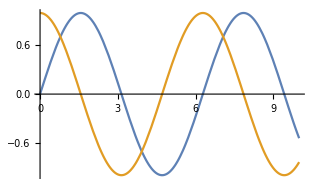
```mathematica
-Graphics-
Button["Click Here",Print[10!]]
```

-Graphics-

```mathematica
"Click Here"
Button["Click Here",Print[10!]]
```

Click Here

Click Here

```mathematica
Button["Click Here",Print[10!]]
```

Click Here

```mathematica
Button["Click Here",Print[Ciao]]
```

Click Here

Ciao

Ciao

Ciao

«1 more identical outputs»

```mathematica
Table[With[{i=i},Button[i,f[i]]],{i,1,2}]
```

{1,2}

```mathematica
m=RandomVariate[NormalDistribution[],{1000,1000}];

v=RandomVariate[NormalDistribution[],1000];

AbsoluteTiming[Do[MapThread[Prepend,{m,v}],{100}];]
```

{1.55321,Null}

```mathematica
array={{a,1,2},{b,2,3},{c,3,4}};
column={x,y,z};

(*insert as the first column*)
Join[List/@column,array,2]
(*insert as the last column*)
Join[array,List/@column,2]
```

{{x,a,1,2},{y,b,2,3},{z,c,3,4}}

{{a,1,2,x},{b,2,3,y},{c,3,4,z}}

```mathematica
data=SQLExecute[conn1,"SELECT * FROM tesserato"];
data
```

{{1,061537,Andolfo,Angelo,Arbitro regionale giovanile,Regionale - 6a cat.,SQLDateTime[{2019,4,3}],POGGIO RENATICO,FERRARA,EMILIA-ROMAGNA,SQLDateTime[{2002,8,7}],ESTERO,3703279389,bruzzoandolfo@libero.it,2,Poggio Renatico,Null,True,Null,Null,True},357,{427,067896,De Cesare,Lorenzo,Arbitro regionale giovanile,Regionale - 6a cat.,SQLDateTime[{2020,1,15}],Ferrara,FERRARA,EMILIA-ROMAGNA,SQLDateTime[{2006,1,22}],FERRARA,3207277090,lorilego22@gmail.com,2,Ferrara,,True,True,False,False}}
 |  |  |  |

```mathematica
bottoni = {{Button["Click Here",Print[Ciao]]}, {Button["Click Here",Print[Ciao]]},{ Button["Click Here",Print[Ciao]]}}
```

{{Click Here},{Click Here},{Click Here}}

```mathematica
tabellaJoin = Join[data, List@bottoni, 2]
```

{{1,061537,Andolfo,Angelo,Arbitro regionale giovanile,Regionale - 6a cat.,SQLDateTime[{2019,4,3}],POGGIO RENATICO,FERRARA,EMILIA-ROMAGNA,SQLDateTime[{2002,8,7}],ESTERO,3703279389,bruzzoandolfo@libero.it,2,Poggio Renatico,Null,True,Null,Null,True,{Click Here},{Click Here},{Click Here}},357,{427,067896,De Cesare,Lorenzo,Arbitro regionale giovanile,Regionale - 6a cat.,SQLDateTime[{2020,1,15}],Ferrara,FERRARA,EMILIA-ROMAGNA,SQLDateTime[{2006,1,22}],FERRARA,3207277090,lorilego22@gmail.com,2,Ferrara,,True,True,False,False}}
 |  |  |  |

```mathematica
TableForm[tabellaJoin]
```

1 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 2 | Poggio Renatico | Null | True | Null | Null | True | Click Here | Click Here | Click Here
2 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 2 | Ferrara | NO partite tardi | True | False | False | False |  |  | 
3 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 2 | Ferrara |  | False | False | False | True |  |  | 
4 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
5 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
6 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
7 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
8 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 2 | Santa M. M. |  | True | False | False | False |  |  | 
9 | 065109 | Bottura | Giorgio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
10 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,23}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 2 | Cento | Null | True | Null | Null | Null |  |  | 
11 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 2 | Ferrara | Null | False | Null | Null | Null |  |  | 
12 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 2 | Cento | Null | True | Null | Null | Null |  |  | 
13 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C con deroga A2/F | SQLDateTime[{2019,8,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
14 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,13}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 2 | Ferrara | Lun-Ven Ok Inizio A Ferrara Alle 20:00 | True | False | False | True |  |  | 
15 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
16 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,11}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 2 | Cento | Null | True | Null | Null | Null |  |  | 
17 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
18 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,10,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
19 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C con deroga A1/F | SQLDateTime[{2019,9,1}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 2 | Ferrara | Null | True | Null | Null | False |  |  | 
20 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
21 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
22 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,3,6}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
23 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,5}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 2 | Cento | Null | True | Null | Null | True |  |  | 
24 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
25 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 2 | Ferrara | Null | False | False | Null | Null |  |  | 
26 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 2 | Ferrara | Null | True | False | Null | False |  |  | 
27 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 2 | Argenta | Null | True | Null | Null | Null |  |  | 
28 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 2 | Argenta | Null | True | Null | Null | Null |  |  | 
29 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | gabrifregni33@gmail.com | 2 | Terre Del Reno | Null | True | Null | Null | Null |  |  | 
30 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 2 | Ferrara | LAVORA Lun-Sab fino alle 19:30 a Ferrara | True | False | True | True |  |  | 
31 | 051423 | Gava | Alice | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
32 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,6}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 2 | Argenta | Null | True | Null | Null | True |  |  | 
33 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
34 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
35 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
36 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
37 | 049499 | Manzi | Federico | Arbitro Regionale | Serie C | SQLDateTime[{2019,6,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | BENTIVOGLIO | 3387181046 | fede_manzi@libero.it | 2 | Cento |  | True | False | True | True |  |  | 
38 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 2 | Argenta |  | False | False | False | False |  |  | 
39 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,1,23}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 2 | Argenta | Null | True | Null | Null | True |  |  | 
40 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 2 | Ferrara | Null | False | Null | Null | Null |  |  | 
41 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,3,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
42 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,21}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
43 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | MASI TORELLO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 2 | Masi Torello | Null | True | Null | Null | True |  |  | 
44 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
45 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 2 | Cento | Null | False | False | Null | False |  |  | 
46 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 2 | Cento | POCHE PARTITE | True | False | False | True |  |  | 
47 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 2 | Santa M. M. |  | True | False | True | True |  |  | 
48 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 2 | Ferrara | Max 1 partita/weekend, inizio gare infrasettimanali 19:45 - 21:00 | True | False | False | True |  |  | 
49 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
50 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 2 | Ferrara | Null | False | Null | Null | Null |  |  | 
51 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,13}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 2 | Argenta | Null | True | Null | Null | Null |  |  | 
52 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 2 | Cento | Null | True | Null | Null | True |  |  | 
53 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
54 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,24}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
55 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
56 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 2 | Cento | Null | True | Null | Null | True |  |  | 
64 | 059472 | Albieri | Sofia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,26}] | FERRARA | 3357090468 | dott.sofia.albieri@gmail.com | 2 | Ferrara | Lavora fino alle 18:00 | True | False | False | True |  |  | 
65 | 053437 | Angelini | Giada | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,13}] | BOLOGNA | 3474379920 | angelinigiada96@gmail.com | 2 | Cento | Null | True | Null | Null | True |  |  | 
66 | 060043 | Attanasio | Anna Chiara | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,20}] | MESAGNE | 3808679765 | angela.giuseppe.anna@hotmail.it | 2 | Argenta | Null | False | False | Null | False |  |  | 
67 | 059473 | Baraldi | Nicola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,1,7}] | FERRARA | 3491844763 | baraldinicola@yahoo.it | 2 | Ferrara | Null | False | Null | Null | True |  |  | 
68 | 061229 | Benazzi | Eugenio | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,2,9}] | CENTO | 3473090508 | benazzi89@gmail.com | 2 | Cento | Null | True | Null | Null | True |  |  | 
69 | 060044 | Biancofiore | Paola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,3,1}] | SAN SEVERO | 3495529123 | lorenzobosco71@libero.it | 2 | Santa M. M. |  | True | False | False | False |  |  | 
70 | 064771 | Bolzonaro | Sara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,22}] | FERRARA | 3485434305 | sara.bolzonaro93@gmail.com | 2 | Ferrara | NO PARTITE DA SOLA | True | False | False | False |  |  | 
71 | 063403 | Caselli | Giacomo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,11,16}] | FERRARA | 3404114897 | jackcase@hotmail.it | 2 | Ferrara |  | True | False | False | True |  |  | 
72 | 053438 | Collaro | Giorgia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,7,31}] | DOLO | 3349241748 | gio.collaro@alice.it | 2 | Ferrara | SOLO partite a Ferrara | True | False | False | False |  |  | 
73 | 059474 | Cristofori | Michela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,3,17}] | FERRARA | 3425046135 | cristofori1703@libero.it | 2 | Ferrara | LAVORA fino alle 19:00 | True | False | False | True |  |  | 
74 | 064770 | De Palo | Beatrice | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,3,2}] | FERRARA | 3473123570 | bea.depalo@gmail.com | 2 | Ferrara | Lavora fino alle 18:30 | True | False | False | False |  |  | 
75 | 063300 | Favero | Cristina | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,9,25}] | FERRARA | 3472572153 | cris74.cf@gmail.com | 2 | Cento |  | True | False | False | True |  |  | 
76 | 063408 | Fiocchi | Greta | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,1,4}] | CENTO | 3466268195 | greta.fiocchi@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
77 | 054049 | Genovese | Franco | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1954,2,21}] | GAMBATESA | 3384612457 | franco.geno@libero.it | 2 | Cento | Null | True | Null | Null | True |  |  | 
78 | 040278 | Gentili | Chiara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,9,19}] | CENTO | 3477217162 | gentili_chiara@libero.it | 2 | Ferrara | Null | False | False | Null | False |  |  | 
79 | 050224 | Guadalupi | Carlotta | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,16}] | BRINDISI | 3478870368 | carlotta-16@libero.it | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
80 | 053444 | Guselli | Leonardo | UDC Nazionale | Nazionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,1,5}] | CENTO | 3474980827 | leogus92@gmail.com | 2 | Cento | LAVORA a Cento fino alle 18:00 | True | False | False | True |  |  | 
81 | 063295 | Imparato | Leonardo | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,7,31}] | NAPOLI | 3495332103 | lor3067@live.it | 2 | Ferrara | Null | False | Null | Null | True |  |  | 
82 | 064603 | Lamborghini | Silvia | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,3,9}] | CENTO | 3492901835 | silvialamborghini95@gmail.com | 2 | Cento | Lun-Ven SOLO dalle 19:30 | True | False | False | False |  |  | 
83 | 053451 | Magistro | Nunzio | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1976,7,24}] | MATERA | 3396084984 | numaggi@yahoo.it | 2 | Ferrara | Lavora fino alle 18:30 | True | False | False | True |  |  | 
84 | 060048 | Magnani | Camilla | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,18}] | LUGO | 3481189990 | magnani.cami@gmail.com | 2 | Argenta | Null | True | Null | Null | Null |  |  | 
85 | 042445 | Maiella | Maria | UDC Nazionale | Nazionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1988,8,2}] | CAMPOBASSO | 3347561136 | mary_dieci@hotmail.it | 2 | Ferrara | LAVORA a Ferrara fino alle 17:00 | True | False | False | True |  |  | 
86 | 064599 | Mandrioli | Anna | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,2,16}] | CENTO | 3485977173 | mandrioli.anna@gmail.com | 2 | Cento | Lun-Ven può arrivare sui campi alle 19:00 | False | False | False | False |  |  | 
87 | 061225 | Marchetti | Cristiana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,12,22}] | OSIMO | 3396680097 | cristiana.marchetti0@gmail.com | 2 | Ferrara | Lun-Ven può arrivare sui campi alle 21:00 | False | False | False | False |  |  | 
88 | 061230 | Messina | Giuliana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,5,12}] | ERICE | 3409138240 | giulianamessina1992@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
89 | 053447 | Milani | Alessia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,3,9}] | FERRARA | 3479247643 | alessiamilani@live.it | 2 | Ferrara | NO TRASFERTE | True | False | False | False |  |  | 
90 | 063406 | Paganelli | Eleonora | UDC Regionale | Regionale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,7,25}] | BENTIVOGLIO | 3466050522 | paganelli.eleonora@gmail.com | 2 | Terre Del Reno | Null | True | Null | Null | Null |  |  | 
91 | 045162 | Pasquali | Francesco | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,12,22}] | FERRARA | 3392856602 | fpasquali73@gmail.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
92 | 050123 | Pedrazzi | Roberto | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,3,12}] | FERRARA | 3393437868 | robertopedro@alice.it | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
93 | 056472 | Piccinini | Andrea | UDC Regionale | Regionale | Null | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,5,7}] | BOLOGNA | 3664518518 | apiccinini2003@yahoo.it | 2 | Poggio Renatico | Null | True | Null | Null | True |  |  | 
94 | 030485 | Profili | Carlo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,10,19}] | FERRARA | 3388506294 | cprofili@vmmotori.com | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
95 | 053427 | Rodolfi | Irene | UDC Amatoriale | Amatoriale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,2,20}] | FERRARA | 3474365650 | irenerodolfi@alice.it | 2 | Terre Del Reno | Null | False | Null | Null | Null |  |  | 
96 | 050122 | Tabanelli | Claudio | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1964,12,23}] | FORLI' | 3476419333 | 710068@vodafone.it | 2 | Ferrara | Null | True | Null | Null | True |  |  | 
97 | 059478 | Totero | Daniela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,9,1}] | VIMERCATE | 3385637937 | toterodany@yahoo.it | 2 | Ferrara | NO Lun - Ven | True | False | False | True |  |  | 
98 | 064772 | Tremamunno | Valentina | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,10,5}] | FERRARA | 3389778206 | valevale.911@gmail.com | 2 | Ferrara | Lun - Sab SOLO dalle 16:00 | True | False | False | False |  |  | 
99 | 054906 | Vitelletti | Maria Letizia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1989,10,3}] | FERRARA | 3295354763 | leti.vitelletti@libero.it | 2 | Ferrara | Null | False | False | Null | False |  |  | 
100 | 025043 | Zabini | Carlotta | UDC Nazionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,9,19}] | FERRARA | 3290509692 | carlottazabini@virgilio.it | 2 | Ferrara | Null | False | Null | Null | Null |  |  | 
101 | 050121 | Zanardi | Francesca | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,9,4}] | FERRARA | 3343511332 | frencizanardi@gmail.com | 2 | Ferrara | Null | False | False | Null | False |  |  | 
102 | 061227 | Zanardi | Virginia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,15}] | COMACCHIO | 3457639091 | zanardivirginia1@gmail.com | 2 | Ferrara | Disponibile DALLE 18.30 per Università | True | False | False | False |  |  | 
127 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 3 | Poggio Renatico | Null | True | Null | Null | Null |  |  | 
128 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,13}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
129 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2018,8,28}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
130 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,12,11}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
131 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
132 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
133 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
134 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
135 | 065109 | Bottura | Giorgio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,12}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
136 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,25}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
137 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
138 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,10,3}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
139 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,7}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
140 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,9,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
141 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,24}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
142 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,19}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
143 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
144 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,10,22}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
145 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,1}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
146 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,9,26}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
147 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
148 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,27}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
149 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2018,7,26}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
150 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
151 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2018,7,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
152 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2018,7,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
153 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
154 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
155 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | giovannifregni@yahoo.it | 3 | Terre Del Reno | Null | True | Null | Null | Null |  |  | 
156 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
157 | 051423 | Gava | Alice | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
158 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,13}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
159 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
160 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,8}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
161 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2018,11,28}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
162 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,12,20}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
163 | 049499 | Manzi | Federico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,6,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | CENTO | 3387181046 | fede_manzi@libero.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
164 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
165 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,2,11}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
166 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
167 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
168 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,22}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
169 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,16}] | MASI TORELLO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 3 | Masi Torello | Null | True | Null | Null | Null |  |  | 
170 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
171 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2018,9,2}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
172 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
173 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
174 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
175 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,13}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
176 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
177 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,14}] | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
178 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
179 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,12}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@fastwebnet.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
180 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,1,8}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
181 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,2,19}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
182 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2018,7,26}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
183 | 059472 | Albieri | Sofia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,26}] | FERRARA | 3357090468 | dott.sofia.albieri@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
184 | 053437 | Angelini | Giada | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,13}] | BOLOGNA | 3474379920 | angelinigiada96@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
185 | 060043 | Attanasio | Anna Chiara | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,20}] | MESAGNE | 3808679765 | angela.giuseppe.anna@hotmail.it | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
186 | 059473 | Baraldi | Nicola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,1,7}] | FERRARA | 3491844763 | baraldinicola@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
187 | 061229 | Benazzi | Eugenio | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,2,9}] | CENTO | 3473090508 | benazzi89@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
188 | 060044 | Biancofiore | Paola | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,3,1}] | SAN SEVERO | 3495529123 | lorenzobosco71@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
189 | 064771 | Bolzonaro | Sara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,22}] | FERRARA | 3485434305 | sara.bolzonaro93@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
190 | 063403 | Caselli | Giacomo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,11,16}] | FERRARA | 3404114897 | jackcase@hotmail.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
191 | 053438 | Collaro | Giorgia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,7,31}] | DOLO | 3349241748 | gio.collaro@alice.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
192 | 059474 | Cristofori | Michela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,3,17}] | FERRARA | 3425046135 | cristofori1703@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
193 | 064770 | De Palo | Beatrice | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,3,2}] | FERRARA | 3473123570 | bea.depalo@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
194 | 063300 | Favero | Cristina | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,9,25}] | FERRARA | 3472572153 | cris74.cf@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
195 | 063408 | Fiocchi | Greta | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,1,4}] | CENTO | 3466268195 | greta.fiocchi@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
196 | 054049 | Genovese | Franco | UDC Amatoriale | Amatoriale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1954,2,21}] | GAMBATESA | 3384612457 | franco.geno@libero.it | 3 | Cento | Null | True | Null | Null | Null |  |  | 
197 | 040278 | Gentili | Chiara | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,9,19}] | CENTO | 3477217162 | gentili_chiara@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
198 | 050224 | Guadalupi | Carlotta | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,16}] | BRINDISI | 3478870368 | carlotta-16@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
199 | 053444 | Guselli | Leonardo | UDC Nazionale | Nazionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,1,5}] | CENTO | 3474980827 | leogus92@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
200 | 063295 | Imparato | Leonardo | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,7,31}] | NAPOLI | 3495332103 | lor3067@live.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
201 | 064603 | Lamborghini | Silvia | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,3,9}] | CENTO | 3492901835 | silvialamborghini95@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
202 | 053451 | Magistro | Nunzio | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1976,7,24}] | MATERA | 3396084984 | numaggi@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
203 | 060048 | Magnani | Camilla | UDC Regionale | Regionale | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,18}] | LUGO | 3481189990 | magnani.cami@gmail.com | 3 | Argenta | Null | True | Null | Null | Null |  |  | 
204 | 042445 | Maiella | Maria | UDC Nazionale | Nazionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1988,8,2}] | CAMPOBASSO | 3347561136 | mary_dieci@hotmail.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
205 | 064599 | Mandrioli | Anna | UDC Regionale | Regionale | Null | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1985,2,16}] | CENTO | 3485977173 | mandrioli.anna@gmail.com | 3 | Cento | Null | True | Null | Null | Null |  |  | 
206 | 061225 | Marchetti | Cristiana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,12,22}] | OSIMO | 3396680097 | cristiana.marchetti0@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
207 | 061230 | Messina | Giuliana | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1992,5,12}] | ERICE | 3409138240 | giulianamessina1992@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
208 | 053447 | Milani | Alessia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,3,9}] | FERRARA | 3479247643 | alessiamilani@live.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
209 | 063406 | Paganelli | Eleonora | UDC Regionale | Regionale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,7,25}] | BENTIVOGLIO | 3466050522 | paganelli.eleonora@gmail.com | 3 | Terre Del Reno | Null | True | Null | Null | Null |  |  | 
210 | 045162 | Pasquali | Francesco | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,12,22}] | FERRARA | 3392856602 | fpasquali73@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
211 | 050123 | Pedrazzi | Roberto | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,3,12}] | FERRARA | 3393437868 | robertopedro@alice.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
212 | 056472 | Piccinini | Andrea | UDC Regionale | Regionale | Null | POGGIO RENATICO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1973,5,7}] | BOLOGNA | 3664518518 | apiccinini2003@yahoo.it | 3 | Poggio Renatico | Null | True | Null | Null | Null |  |  | 
213 | 030485 | Profili | Carlo | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,10,19}] | FERRARA | 3388506294 | cprofili@vmmotori.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
214 | 053427 | Rodolfi | Irene | UDC Amatoriale | Amatoriale | Null | TERRE DEL RENO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1971,2,20}] | FERRARA | 3474365650 | irenerodolfi@alice.it | 3 | Terre Del Reno | Null | True | Null | Null | Null |  |  | 
215 | 050122 | Tabanelli | Claudio | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1964,12,23}] | FORLI' | 3476419333 | 710068@vodafone.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
216 | 059478 | Totero | Daniela | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,9,1}] | VIMERCATE | 3208187663 | toterodany@yahoo.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
217 | 064772 | Tremamunno | Valentina | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,10,5}] | FERRARA | 3389778206 | valevale.911@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
218 | 054906 | Vitelletti | Maria Letizia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1989,10,3}] | FERRARA | 3295354763 | leti.vitelletti@libero.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
219 | 025043 | Zabini | Carlotta | UDC Nazionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1975,9,19}] | FERRARA | 3290509692 | carlottazabini@virgilio.it | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
220 | 050121 | Zanardi | Francesca | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,9,4}] | FERRARA | 3343511332 | frencizanardi@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
221 | 061227 | Zanardi | Virginia | UDC Regionale | Regionale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,15}] | COMACCHIO | 3457639091 | zanardivirginia1@gmail.com | 3 | Ferrara | Null | True | Null | Null | Null |  |  | 
222 | 040329 | Rovigatti | Franco | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,28}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,10,9}] | FERRARA | 3288517814 | sheva8889@libero.it | 2 | Ferrara | NO Caravita | False | False | False | True |  |  | 
223 | 063290 | Iavarone | Carmine | UDC Amatoriale | Amatoriale | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,9,11}] | NAPOLI | 3338232569 | iavar1@alice.it | 2 | Ferrara | LAVORA fino alle 18:00 | True | False | False | False |  |  | 
224 | 060353 | Baraldi | Anna | Null | Null | Null | Null | Null | Null | SQLDateTime[{1996,4,2}] | Null | 3479992062 | annafrancesca.baraldi@gmail.com | 2 | Modena |  | True | False | False | False |  |  | 
225 | 002992 | Atti | Paolo | UDC Benemerito | Benemerito | Null | ARGENTA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1947,4,22}] | ARGENTA | non disponibile | non disponibile | 2 | Argenta | Null | False | False | Null | False |  |  | 
226 | 001307 | Rescazzi | Filippo | UDC Benemerito | Benemerito | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1923,11,12}] | BONDENO | non disponibile | ric53@libero.it | 2 | Ferrara | Null | False | False | Null | False |  |  | 
227 | 012869 | Rivaroli | Giulio | UDC Benemerito | Benemerito | Null | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1953,1,18}] | FERRARA | non disponibile | presidente.fe@fip.it | 2 | Ferrara | Null | False | False | Null | False |  |  | 
228 | 002358 | Sivieri | Giancarlo | UDC Benemerito | Benemerito | Null | VIGARANO MAINARDA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1933,5,16}] | FERRARA | non disponibile | jerrysivieri@gmail.com | 2 | Vigarano Mainarda | Null | False | False | Null | False |  |  | 
229 | 019971 | Bassi | Alessandro | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2001,6,19}] | COPPARO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1960,8,26}] | COPPARO | 3396837670 | ales.bas@katamail.com | 2 | Copparo | Null | False | False | Null | False |  |  | 
230 | 057646 | Govoni | Enrico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,4,15}] | CENTO | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | CENTO | 3481189978 | enry.govoni@gmail.com | 2 | Cento | Null | True | Null | Null | Null |  |  | 
231 | 004264 | Menatti | Lorenzo | Arbitro Benemerito | Benemerito | SQLDateTime[{1996,12,31}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1951,9,1}] | FERRARA | non disponibile | ilpennello.arte@libero.it | 2 | Ferrara | Null | False | False | Null | False |  |  | 
232 | 006178 | Menatti | Maurizio | Arbitro Benemerito | Benemerito | SQLDateTime[{2003,7,21}] | FERRARA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1946,9,4}] | FERRARA | 335426691 | maurizio.menatti@gmail.com | 2 | Ferrara | Null | False | False | Null | False |  |  | 
233 | 018708 | Sivieri | Marco | Arbitro Benemerito | Benemerito | SQLDateTime[{2014,7,14}] | VIGARANO MAINARDA | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,10,30}] | FERRARA | 3313779338 | jerrysivieri@gmail.com | 2 | Vigarano Mainarda | Null | False | False | Null | False |  |  | 
234 | 066226 | Baraldi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2003,3,31}] | MIRANDOLA | 3462886607 | francescobaraldi31@gmail.com | 4 | Mirandola |  | True | False | False | False |  |  | 
235 | 057791 | Barigazzi | Stefano | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,30}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1997,4,5}] | REGGIO NELL'EMILIA | 3383246591 | ste97_1@libero.it | 4 | Carpi | Null | True | Null | Null | Null |  |  | 
238 | 029382 | Benatti | Paolo | Arbitro Nazionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,19}] | MEDOLLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1979,9,1}] | MIRANDOLA | 3484403571 | paolo_benatti1979@libero.it | 4 | Medolla | Null | True | Null | Null | Null |  |  | 
240 | 064154 | Boba | Skerdi | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,1,23}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,9}] | CARPI | 3401686526 | skerdi.boba@gmail.com | 4 | Carpi | Null | False | False | Null | False |  |  | 
242 | 061240 | Borgato | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | CAMPOSANTO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,11,17}] | MODENA | 3932041608 | matteoborgato46@gmail.com | 4 | Camposanto |  | True | False | False | False |  |  | 
244 | 053795 | Campedelli | Matteo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,12,21}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,20}] | CARPI | 3337772310 | matteo.ca.11@hotmail.it | 4 | Carpi |  | True | False | False | False |  |  | 
245 | 032702 | Cascioli | Donato | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,2,11}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1980,11,15}] | FOGGIA | 3391822363 | dennycasc@hotmail.it | 4 | Carpi |  | True | False | False | False |  |  | 
247 | 061547 | Corsini | Oliver | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,11,27}] | SAVIGNANO SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,12,23}] | PAVULLO NEL FRIGNANO | 3286534527 | corsinioliver@gmail.com | 4 | Savignano Sul Panaro | Null | False | Null | Null | Null |  |  | 
251 | 045412 | Dargenio | Raffaele | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,26}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1994,5,23}] | CARPI | 3407338958 | raffa-94@live.it | 4 | Carpi | Null | True | Null | Null | Null |  |  | 
252 | 054017 | De Santis | Daniele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,29}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,16}] | CASERTA | 3491200086 | daniele.desantis98@gmail.com | 4 | Carpi | Null | True | Null | Null | Null |  |  | 
253 | 063913 | Di Giovanni | Andrea | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,7,19}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1987,9,27}] | PESCARA | 3287369743 | adrdgv@msn.com | 4 | Modena |  | True | False | False | False |  |  | 
254 | 022592 | Di Napoli | Armando | Arbitro Nazionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,6,7}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1973,11,23}] | NAPOLI | 3487402123 | dinarma73@gmail.com | 4 | Modena | Null | True | False | Null | False |  |  | 
255 | 050611 | Donno | Elena | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,9,4}] | CASTELNUOVO RANGONE | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1980,11,14}] | ESTERO | 3383475534 | elenadonno@gmail.com | 4 | Castelnuovo Rangone | Null | True | Null | Null | Null |  |  | 
257 | 034279 | Ferrari | Gianluca | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,26}] | CASTELFRANCO EMILIA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1983,4,9}] | CASTELFRANCO EMILIA | 3396563486 | ferro.int@libero.it | 4 | Castelfranco Emilia | Null | True | Null | Null | Null |  |  | 
259 | 040501 | Fontanini | Pietro | Arbitro Nazionale | Regionale - 6a cat. | SQLDateTime[{2019,6,20}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1986,12,30}] | MODENA | 3299127615 | fontapie@fastwebnet.it | 4 | Modena | Null | True | False | Null | False |  |  | 
260 | 061548 | Franchi | Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,15}] | CASTELFRANCO EMILIA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,10,29}] | CASTELFRANCO EMILIA | 3357177057 | antosamefranchi@gmail.com | 4 | Castelfranco Emilia |  | False | False | False | False |  |  | 
261 | 061239 | Frigieri | Dennys | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,26}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,6,15}] | MODENA | 3311104217 | frigieri57@gmail.com | 4 | San Felice Sul Panaro | Null | True | Null | Null | Null |  |  | 
263 | 065660 | Garello | Tommaso Edoardo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,15}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,11,15}] | SCANDIANO | 3474854429 | TOMMYGARELLO@GMAIL.COM | 4 | Sassuolo |  | True | False | False | False |  |  | 
266 | 061242 | Hamdi | Azmi | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2000,12,27}] | MIRANDOLA | 3282409462 | hmd27az@gmail.com | 4 | San Felice Sul Panaro |  | True | False | False | False |  |  | 
267 | 042211 | Iuppa | Antonio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,14}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1988,3,17}] | PALERMO | 3807505613 | antonio.iuppa@gmail.com | 4 | Modena |  | True | False | False | False |  |  | 
269 | 065661 | Levizzani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,6,5}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,5,13}] | REGGIO NELL'EMILIA | 3421918037 | LEVIZZANI.FRANCESCO@GMAIL.COM | 4 | Sassuolo | Null | False | Null | Null | Null |  |  | 
271 | 066508 | Macchioni | Elisabetta | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,23}] | SAN FELICE SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2005,4,7}] | MIRANDOLA | 3315650034 | lauragolinelli@gmail.com | 4 | San Felice Sul Panaro |  | True | False | False | False |  |  | 
273 | 061273 | Marescotti | Mirko | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,23}] | PAVULLO NEL FRIGNANO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1985,10,18}] | PAVULLO NEL FRIGNANO | 3341711001 | mitchmarescotti@hotmail.it | 4 | Pavullo Nel Frignano |  | True | False | False | False |  |  | 
274 | 037077 | Marino | Antonio | Arbitro Nazionale | Serie C | SQLDateTime[{2019,7,19}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1983,10,11}] | ATRIPALDA | 3491460569 | marinoantonio11@gmail.com | 4 | Carpi | Null | True | Null | Null | Null |  |  | 
277 | 041549 | Monni | Federico | Arbitro Nazionale | Serie C | SQLDateTime[{2017,10,2}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1990,10,2}] | CAGLIARI | 3924825863 | federico.monni2@gmail.com | 4 | Modena | Null | False | False | Null | False |  |  | 
279 | 028823 | Paradiso | Simone | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,22}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1979,4,11}] | TORINO | 3477508743 | s.paradiso@libero.it | 4 | Modena |  | True | False | False | False |  |  | 
281 | 061955 | Pizzirani | Mirco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,9}] | SAVIGNANO SUL PANARO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,19}] | BOLOGNA | 3384659794 | tania.giglioli@alice.it | 4 | Savignano Sul Panaro |  | True | False | False | False |  |  | 
283 | 053523 | Pongiluppi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,26}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1998,12,17}] | CARPI | 3450772784 | filippo.pongiluppi@gmail.com | 4 | Mirandola | Null | True | Null | Null | Null |  |  | 
285 | 009750 | Ragusa | Valerio | Arbitro Nazionale | Regionale - 6a cat. | SQLDateTime[{2019,6,13}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1959,1,29}] | CASAGIOVE | 3356327469 | valerioragusa@alice.it | 4 | Modena | Null | True | Null | Null | Null |  |  | 
287 | 048775 | Sancilio | Mattia | Arbitro Regionale | Serie C | SQLDateTime[{2018,10,9}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1995,1,27}] | BRINDISI | 3494179211 | mat95_27@hotmail.it | 4 | Modena | Null | False | False | Null | False |  |  | 
290 | 064160 | Schiavi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,10}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2002,11,8}] | CARPI | 3661755270 | fre.schiavi@gmail.com | 4 | Carpi |  | True | False | False | False |  |  | 
292 | 059426 | Tancredi | Giacomo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2017,1,12}] | MODENA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1988,7,27}] | ORTONA | 3283018296 | giacredi@gmail.com | 4 | Modena | Null | False | False | Null | False |  |  | 
293 | 027958 | Tarallo | Giorgio | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,24}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1976,12,21}] | NAPOLI | 3387812757 | giorgio.tarallo76@teletu.it | 4 | Sassuolo | Null | True | Null | Null | Null |  |  | 
295 | 045424 | Toksoy | Ogulcan Hidir | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,10}] | CARPI | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1993,1,12}] | CARPI | 3477878882 | ogulcan06@hotmail.it | 4 | Carpi |  | True | False | False | False |  |  | 
296 | 066232 | Tommasino | Luca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,20}] | MIRANDOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,8}] | MIRANDOLA | 3472762293 | luca.nba04@gmail.com | 4 | Mirandola |  | True | False | False | False |  |  | 
297 | 022699 | Toschi | Davide | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,7,1}] | VIGNOLA | MODENA | EMILIA-ROMAGNA | SQLDateTime[{1974,4,29}] | MODENA | 3492206900 | toschi.davide@tiscalinet.it | 4 | Vignola | Null | True | Null | Null | Null |  |  | 
300 | 065663 | Varni | Carlotta | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,8,22}] | SASSUOLO | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,2}] | SASSUOLO | 3458813649 | VARNICARLOTTA@GMAIL.COM | 4 | Sassuolo |  | True | False | False | False |  |  | 
301 | 065664 | Vecchie' | Davide | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,29}] | FORMIGINE | MODENA | EMILIA-ROMAGNA | SQLDateTime[{2001,11,19}] | FORMIGINE | 3665217410 | DAVIDEVECCHIE@GMAIL.COM | 4 | Formigine | Null | True | Null | Null | Null |  |  | 
302 | 065107 | Boldrini | Federico | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,12}] | FERRARA | 3381333057 | boldrinifederico2001@gmail.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
303 | 064593 | Piro | Emanuele | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,3,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,1,10}] | GALLIPOLI | 3701235747 | emanuelepiro0@gmail.com | 2 | Ferrara | Lun-Gio SOLO dalle 18:30 | True | False | False | False |  |  | 
306 | 066234 | Macchioni | Gianmaria | Null | Null | SQLDateTime[{2019,8,15}] | Null | Null | Null | Null | Null | Null | Null | 4 | mirandola |  | True | False | False | False |  |  | 
307 | 0 | Alberti | Alessandro | Null | Null | SQLDateTime[{2020,1,3}] | Null | Null | Null | Null | Null | 3389825046 | alessandroalberti11@gmail.com | 2 | Argenta |  | True | False | False | False |  |  | 
308 | 0 | Alberti | Davide | Null | Null | SQLDateTime[{2018,12,30}] | Null | Null | Null | Null | Null | 3319053721 | davidealberti098@gmail.com | 2 | Argenta |  | True | False | False | False |  |  | 
309 | 0 | Barlati | Martina | Null | Null | Null | Null | Null | Null | Null | Null | 3486050310 | martina.barlati@gmail.com | 2 | Ferrara |  | True | False | False | False |  |  | 
310 | 0 | Bosi | Leonardo | Null | Null | SQLDateTime[{2019,2,8}] | Null | Null | Null | Null | Null | 3460923991 | leobosi@hotmail.it | 2 | Ferrara |  | True | False | False | False |  |  | 
311 | 0 | Faggioli | Marco | Null | Null | Null | Null | Null | Null | Null | Null | 3313511494 | faggio97.m@libero.it | 2 | Argenta |  | False | False | False | False |  |  | 
312 | 0 | Favot | Enrico | Null | Null | Null | Null | Null | Null | Null | Null | 3897957027 | enrico.favot@yahoo.it | 2 | Ferrara |  | True | False | False | False |  |  | 
313 | 0 | Franchella | Francesco | Null | Null | SQLDateTime[{2018,11,13}] | Null | Null | Null | Null | Null | 3420484017 | franchella.francesco@gmail.com | 2 | Ferrara |  | True | False | False | False |  |  | 
314 | 0 | Marianti Spadoni  | Lorenzo | Null | Null | Null | Null | Null | Null | Null | Null | 3347642081 | marianti.lorenzo@gmail.com | 2 | Ferrara |  | True | False | False | False |  |  | 
315 | 0 | Mennitti | Daniele | Null | Null | Null | Null | Null | Null | Null | Null | 3279470038 | daniele.mennitti@yahoo.it | 2 | Poggio Renatico |  | True | False | False | False |  |  | 
316 | 0 | Okorocha | Gloria | Null | Null | SQLDateTime[{2019,10,29}] | Null | Null | Null | Null | Null | 3331225534 | amargorao@yahoo.it | 2 | Ferrara |  | True | False | False | False |  |  | 
317 | 0 | Piselli | Marco | Null | Null | SQLDateTime[{2018,9,19}] | Null | Null | Null | Null | Null | 3463629902 | simonecortesi8@gmail.com | 2 | Ferrara |  | True | False | False | False |  |  | 
318 | 0 | Piva | Vittorio | Null | Null | SQLDateTime[{2018,11,8}] | Null | Null | Null | Null | Null | 3490066238 | vittorio.piva@live.it | 2 | Ferrara |  | True | False | False | False |  |  | 
319 | 0 | Vaianella | Matteo | Null | Null | SQLDateTime[{2018,11,2}] | Null | Null | Null | Null | Null | 3491301140 | vaia19893@gmail.com | 2 | Ferrara |  | True | False | False | False |  |  | 
320 | 067317 | Candito | Simone | UDC Regionale | Regionale | Null | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,5,22}] | BRINDISI | 3249075391 | lightinslash@gmail.com | 2 | Ferrara |  | True | True | False | False |  |  | 
321 | 067318 | Iavarone | Riccardo | UDC Regionale | Regionale | Null | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,2,21}] | FERRARA | 3396707981 | kobe.mildred@gmail.com | 2 | Ferrara | Lavora Lun-Ven Fino Alle 19:00 | True | True | False | False |  |  | 
322 | 067319 | Mazza | Michele | UDC Regionale | Regionale | Null | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,10,3}] | FERRARA | 3333234711 | michelemazzafe@gmail.com | 2 | Ferrara |  | True | True | False | False |  |  | 
325 | 00000 | Gap Re | Aa | Null | Null | Null | Null | Null | Null | Null | Null |  |  | 4 |  |  | True | False | False | False |  |  | 
326 | 00000 | Gap Bo | Aa | Null | Null | Null | Null | Null | Null | Null | Null |  |  | 4 |  |  | True | False | False | False |  |  | 
327 | 00000 | Gap Fe | Aa | Null | Null | Null | Null | Null | Null | Null | Null |  |  | 4 |  |  | True | False | False | False |  |  | 
329 | 067120 | Canella | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,3}] | FERRARA | 3423244690 | scanella342002@gmail.com | 2 | Ferrara |  | True | True | False | False |  |  | 
330 | 067121 | Carletti | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,9}] | FERRARA | 3703060600 | samy.car9@gmail.com | 2 | Ferrara |  | True | True | False | False |  |  | 
331 | 066996 | Forlani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,20}] | FERRARA | 3888227329 | giantigno@libero.it | 2 | Ferrara |  | True | True | False | False |  |  | 
332 | 066997 | Girotti | Sara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,2}] | CENTO | 3332741220 | sara.girotti@icloud.com | 2 | Cento |  | False | False | False | False |  |  | 
333 | 066998 | Pallotti | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,27}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,3,31}] | LAGOSANTO | 3890429934 | fodericchio@gmail.com | 2 | Argenta |  | True | True | False | False |  |  | 
334 | 066999 | Pola | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,14}] | CENTO | 3337527014 | alepola04@gmail.com | 2 | Alberone |  | True | True | False | False |  |  | 
335 | 067000 | Stabellini | Giacomo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,6}] | Codigoro | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,2,28}] | LAGOSANTO | 3483800748 | monica.mangolini-man@libero.it | 2 | Codigoro |  | True | True | False | False |  |  | 
336 | 067001 | Zanni | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Comacchio | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,22}] | LAGOSANTO | 3317673449 | francesco.zanni2004@gmail.com | 2 | Comacchio |  | True | True | False | False |  |  | 
337 | 066995 | Brunazzi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,11,15}] | LUGO | 3477389129 | luca.brunazzi@gmail.com | 2 | Argenta |  | False | True | False | False |  |  | 
338 | 066994 | Bertocchi | Chiara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,8}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,7,2}] | BENTIVOGLIO | 3883086009 | chiara.bertocchi2003@gmail.com | 2 | Poggio Renatico | Null | True | True | Null | Null |  |  | 
340 | 067089 | Ghazali | Fatima Elisa | Mini UDC | Regionale | Null | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,17}] | ESTERO | 3881932165 | elisaghazali@gmail.com | 2 | Argenta | Null | True | True | Null | Null |  |  | 
341 | 060803 | Fabiano | Flavio | Arbitro Regionale | Serie C | SQLDateTime[{2019,10,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | TARANTO | 3495530054 | flaviofabiano@outlook.com | 2 | Ferrara | Null | True | Null | Null | Null |  |  | 
342 | 067290 | Kica | Enriko | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,10,4}] | LACCO AMENO | 3890462939 | kicaenriko@gmail.com | 2 | Santa M. M. |  | True | True | False | False |  |  | 
344 | 064595 | Rizzo | Mauro | Null | Null | SQLDateTime[{2018,6,27}] | Null | Null | Null | SQLDateTime[{2000,1,19}] | Null | 3662062184 | mauro.rizzo4@gmail.com | 2 | Ferrara |  | True | False | False | False |  |  | 
345 | 067093 | Gardenghi | Carlotta | Mini UDC | Regionale | Null | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,26}] | LAGOSANTO | 3479279777 | carlottadiargenta@gmail.com | 2 | Argenta | Null | True | True | Null | Null |  |  | 
346 | 067748 | Zimelli | Andrea | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2020,2,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,12,12}] | FERRARA | 3474280031 | andreazimelli@gmail.com | 2 | Ferrara | Null | True | True | Null | Null |  |  | 
347 | 061537 | Andolfo | Angelo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,3}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,7}] | ESTERO | 3703279389 | bruzzoandolfo@libero.it | 6 | Poggio Renatico | Null | True | Null | Null | Null |  |  | 
348 | 065110 | Astolfi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,8,29}] | FERRARA | 3493456266 | filippoastolfi7@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
349 | 053147 | Baraldi | Vittorio | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,3,19}] | FERRARA | 3386811742 | vittorio@fbaraldi.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
350 | 057639 | Barbantini | Davide | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,9,15}] | CENTO | 3484127096 | davide.barbantini38@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
351 | 019971 | Bassi | Alessandro | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2001,6,19}] | Copparo | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1960,8,26}] | COPPARO | 3396837670 | ales.bas@katamail.com | 6 | Copparo | Null | True | Null | Null | Null |  |  | 
352 | 066994 | Bertocchi | Chiara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,8}] | Poggio Renatico | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,7,2}] | BENTIVOGLIO | 3883086009 | chiara.bertocchi2003@gmail.com | 6 | Poggio Renatico | Null | True | Null | Null | Null |  |  | 
353 | 065111 | Bianconi | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,11,14}] | FERRARA | 3248085075 | b.marchetti@ausl.fe.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
354 | 065108 | Bidese | Giovanni | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,3,6}] | FERRARA | 3421878749 | gio.bide02@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
355 | 065107 | Boldrini | Federico | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2020,1,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,12}] | FERRARA | 3381333057 | boldrinifederico2001@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
356 | 031520 | Bonetti | Stefano | Arbitro Nazionale | Serie B e A2/F | SQLDateTime[{2019,8,22}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1980,7,20}] | FERRARA | 3384233246 | bonetti.ste@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
357 | 061546 | Bosco | Gaetano Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,3}] | SAN SEVERO | 3427589443 | lorenzobosco71@libero.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
358 | 065109 | Bottura | Giorgio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,1,20}] | COMACCHIO | 3425882749 | botturagiorgio1@libero.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
359 | 066995 | Brunazzi | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,11,15}] | LUGO | 3477389129 | luca.brunazzi@gmail.com | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
360 | 065398 | Bufalo | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,23}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,12,26}] | CENTO | 3384080033 | carmen.yalan@libero.it | 6 | Cento | Null | True | Null | Null | Null |  |  | 
361 | 033771 | Burchi | Leonardo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2015,12,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1982,10,18}] | FERRARA | 3392395160 | leonardo.burchi@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
362 | 067120 | Canella | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,3}] | FERRARA | 3423244690 | scanella342002@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
363 | 065400 | Carascoso | Paolo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,2}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,12}] | CENTO | 3925572505 | giulybriss@libero.it | 6 | Cento | Null | True | Null | Null | Null |  |  | 
364 | 045896 | Caravita | Giulia | Arbitro Regionale | Serie C con deroga A2/F | SQLDateTime[{2019,8,7}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,28}] | FERRARA | 3487042175 | giulia.caravita@me.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
365 | 067121 | Carletti | Samuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,12,9}] | FERRARA | 3703060600 | samy.car9@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
366 | 035817 | Cenedese | Maurizio | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,10,13}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1968,11,18}] | BERGAMO | 3280669904 | cenedese.maurizio@inwind.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
367 | 060126 | Corbetta | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,21}] | FERRARA | 3423859778 | tommaso.corbetta.it@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
368 | 065401 | D'Annunzio | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,11}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,25}] | CENTO | 3925782085 | umbertodannunzio@libero.it | 6 | Cento | Null | True | Null | Null | Null |  |  | 
369 | 051874 | De Palo | Tommaso | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1997,9,30}] | FERRARA | 3489233371 | tommy.depo@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
370 | 059971 | Di Marco | Luca | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,10,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,5,31}] | ATESSA | 3297168488 | lucadm24@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
371 | 045816 | Di Marco | Rebecca | Arbitro Regionale | Serie C con deroga A1/F | SQLDateTime[{2019,9,1}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1993,7,19}] | PESCARA | 3337885611 | rebecca.dimarco@hotmail.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
372 | 065719 | Ercolini | Filippo | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,9,26}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,6,13}] | FERRARA | 3349919128 | pippo.ercolini@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
373 | 060803 | Fabiano | Flavio | Arbitro Regionale | Serie C | SQLDateTime[{2019,10,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | TARANTO | 3495530054 | flaviofabiano@outlook.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
374 | 057641 | Fiocchi | Filippo | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,4}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,8,19}] | CENTO | 3663407857 | filippofiocchi1@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
375 | 061539 | Fiocchi | Enrico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,27}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,6,18}] | CENTO | 3466364880 | fiocchi.enrico@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
376 | 051441 | Fiocchi | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,5}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1996,4,2}] | CENTO | 3404020477 | leo.fiocchi@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
377 | 054924 | Fioriti | Andrea | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,2}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,7,14}] | VASTO | 3314586933 | afioriti98@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
378 | 020882 | Flammini | Paolo | Arbitro Fuori Quadro | Fuori Quadro | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
379 | 058867 | Flammini | Paolo | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2019,7,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1966,7,13}] | FERRARA | 3474787635 | paolo.flammini@virgilio.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
380 | 055878 | Forlani | Micol | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,8,29}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,3,31}] | COMACCHIO | 3337380188 | miniroma1999@libero.it | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
381 | 058136 | Forlani | Manuele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,2}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,10,22}] | COMACCHIO | 3669319236 | miniroma2000@libero.it | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
382 | 066996 | Forlani | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,29}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,7,20}] | FERRARA | 3888227329 | giantigno@libero.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
383 | 065402 | Fregni | Gabriele | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,5,29}] | Terre Del Reno | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,16}] | CENTO | 3270616803 | gabrifregni33@gmail.com | 6 | Terre Del Reno | Null | True | Null | Null | Null |  |  | 
384 | 048453 | Fusetti | Leonardo | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1994,6,24}] | FERRARA | 3386999775 | leonardo.fusetti94@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
385 | 051423 | Gava | Alice | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,24}] | FERRARA | 3331002130 | gavaalice@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
386 | 042259 | Gennari | Carlo Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,6}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1990,3,12}] | PORTOMAGGIORE | 3483848198 | c.a_gennari@libero.it | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
387 | 063576 | Giannasi | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,2,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2003,4,7}] | CENTO | 3276956212 | lorygiannasi@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
388 | 066997 | Girotti | Sara | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,30}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,1,2}] | CENTO | 3332741220 | sara.girotti@icloud.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
389 | 060122 | Golfieri | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,4}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,24}] | FERRARA | 3669738494 | marcyandy@libero.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
390 | 057646 | Govoni | Enrico | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,4,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1999,4,14}] | CENTO | 3481189978 | enry.govoni@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
391 | 059887 | Grazioli | Tommaso | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,11,14}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,2,24}] | CENTO | 3427487967 | tommaso.grazioli00@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
392 | 067290 | Kica | Enriko | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,4,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,10,4}] | LACCO AMENO | 3890462939 | kicaenriko@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
393 | 063747 | La Gatta | Valeria | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,12,20}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,4,8}] | FOGGIA | 3423707606 | valerialagatta08@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
394 | 049499 | Manzi | Federico | Arbitro Regionale | Serie C | SQLDateTime[{2019,6,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,12,13}] | CENTO | 3387181046 | fede_manzi@libero.it | 6 | Cento | Null | True | Null | Null | Null |  |  | 
395 | 004264 | Menatti | Lorenzo | Arbitro Benemerito | Benemerito | SQLDateTime[{1996,12,31}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1951,9,1}] | FERRARA | non disponibile | ilpennello.arte@libero.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
396 | 006178 | Menatti | Maurizio | Arbitro Benemerito | Benemerito | SQLDateTime[{2003,7,21}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1946,9,4}] | FERRARA | 335426691 | maurizio.menatti@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
397 | 065104 | Novelli | Elia | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,3,15}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,8,13}] | CECINA | 3470713171 | novelmarco@yahoo.it | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
398 | 066998 | Pallotti | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,3,14}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,3,31}] | LAGOSANTO | 3890429934 | fodericchio@gmail.com | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
399 | 053145 | Pasetti | Piero | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2020,1,23}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1998,9,4}] | COMACCHIO | 3405634693 | pieropasetti@libero.it | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
400 | 061549 | Pasquali | Tommaso | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2018,9,10}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,12,2}] | FERRARA | 3774590487 | tommypasqua01@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
401 | 047966 | Pedrazzi | Mattia | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2018,10,30}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,4,7}] | FERRARA | 3472661137 | mattia.pedrazzi@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
402 | 064593 | Piro | Emanuele | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,3,11}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,1,10}] | GALLIPOLI | 3701235747 | emanuelepiro0@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
403 | 066999 | Pola | Alessandro | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,10,28}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,5,14}] | CENTO | 3337527014 | alepola04@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
404 | 063577 | Pozzi | Filippo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,11,21}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,9,17}] | CENTO | 3277325208 | filopoz02@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
405 | 034686 | Ragazzi | Lorenzo Maria | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | Masi Torello | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,8,29}] | FERRARA | 3289633728 | lorenzo_mragazzi@yahoo.it | 6 | Masi Torello | Null | True | Null | Null | Null |  |  | 
406 | 022460 | Rambaldi | Michele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,7,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1972,10,17}] | FERRARA | 335433243 | mrambos72@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
407 | 040075 | Resca | Luca | Arbitro Nazionale | Serie C | SQLDateTime[{2019,8,29}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,8,13}] | BENTIVOGLIO | 3334813987 | luca.resca@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
408 | 039980 | Resca | Alberto | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,15}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,7,9}] | BENTIVOGLIO | 3479261531 | alberto.resca@gmail.com | 6 | Cento | Null | True | Null | Null | Null |  |  | 
409 | 055882 | Romanello | Cristian | Arbitro Regionale | Serie C | SQLDateTime[{2019,8,16}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1995,7,2}] | FERRARA | 3496764752 | krystian1284@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
410 | 040329 | Rovigatti | Franco | Arbitro Regionale | Regionale - 6a cat. | SQLDateTime[{2019,1,11}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1987,10,9}] | FERRARA | 3288517814 | sheva8889@libero.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
411 | 039116 | Saletti | Marco | Arbitro Regionale | Serie C | SQLDateTime[{2019,7,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1986,1,8}] | FERRARA | 3478561450 | saletti.marco@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
412 | 060123 | Serra | Federico | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,2,18}] | FERRARA | 3342922781 | stoc36@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
413 | 018708 | Sivieri | Marco | Arbitro Benemerito | Benemerito | SQLDateTime[{2014,7,14}] | Vigarano Mainarda | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1967,10,30}] | FERRARA | 3313779338 | jerrysivieri@gmail.com | 6 | Vigarano Mainarda | Null | True | Null | Null | Null |  |  | 
414 | 067000 | Stabellini | Giacomo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,6}] | Codigoro | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2005,2,28}] | LAGOSANTO | 3483800748 | monica.mangolini-man@libero.it | 6 | Codigoro | Null | True | Null | Null | Null |  |  | 
415 | 034041 | Terranova | Francesco | Arbitro Nazionale | Serie A2 e A1/F | SQLDateTime[{2019,8,19}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1983,1,23}] | RAGUSA | 3937073332 | fterranova83@yahoo.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
416 | 065105 | Trevisan | Luigi Antonio | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,2,13}] | Argenta | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,28}] | LAGOSANTO | 3427813265 | luigitrevisan2004@gmail.com | 6 | Argenta | Null | True | Null | Null | Null |  |  | 
417 | 045077 | Venezia | Raffaele | Arbitro Regionale | Serie D, B/F e C/F - 5a cat. | SQLDateTime[{2019,8,1}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1981,12,16}] | MATERA | 3931213504 | magicoraphaels@yahoo.it | 6 | Cento | Null | True | Null | Null | Null |  |  | 
418 | 058139 | Vigorelli | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,9,5}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2000,9,15}] | VERONA | 3703019024 | lorenzo.vigorellikd35@fastwebnet.it | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
419 | 061551 | Vitali | Matteo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,24}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2002,4,18}] | FERRARA | 3331128321 | maddalena.felloni@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
420 | 065106 | Vivaldi | Gianluca | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2001,9,19}] | FERRARA | 3331134862 | mariamancino28@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
421 | 043341 | Wong | Fabio Ka Kit | Arbitro Regionale | Serie C | SQLDateTime[{2019,9,20}] | Cento | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1991,11,27}] | FIRENZE | 3483744595 | fabiokitkat@hotmail.it | 6 | Cento | Null | True | Null | Null | Null |  |  | 
422 | 067001 | Zanni | Francesco | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2019,12,6}] | Comacchio | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2004,11,22}] | LAGOSANTO | 3317673449 | francesco.zanni2004@gmail.com | 6 | Comacchio | Null | True | Null | Null | Null |  |  | 
423 | 067748 | Zimelli | Andrea | Arbitro Amatoriale | Regionale - 6a cat. | SQLDateTime[{2020,2,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{1974,12,12}] | FERRARA | 3474280031 | andreazimelli@gmail.com | 6 | Ferrara | Null | True | Null | Null | Null |  |  | 
424 | 067597 | Carpi | Francesco | Null | Null | SQLDateTime[{2019,3,7}] | Null | Null | Null | SQLDateTime[{2001,5,1}] | Null |  |  | 4 | Modena |  | True | False | False | False |  |  | 
425 | 067598 | Giacobazzi | Luca | Null | Null | SQLDateTime[{2019,9,11}] | Null | Null | Null | SQLDateTime[{2004,8,30}] | Null |  |  | 4 | Formigine |  | True | False | False | False |  |  | 
426 | 067599 | Romagnoli | Federico | Null | Null | SQLDateTime[{2019,11,22}] | Null | Null | Null | SQLDateTime[{2004,12,19}] | Null |  |  | 4 | Sassuolo |  | True | False | False | False |  |  | 
427 | 067896 | De Cesare | Lorenzo | Arbitro regionale giovanile | Regionale - 6a cat. | SQLDateTime[{2020,1,15}] | Ferrara | FERRARA | EMILIA-ROMAGNA | SQLDateTime[{2006,1,22}] | FERRARA | 3207277090 | lorilego22@gmail.com | 2 | Ferrara |  | True | True | False | False |  |  |

Ciao

```mathematica
(mat={{1,5,8},{2,6,9},{3,7,10},{0,0,0}})//MatrixForm
```

(1 | 5 | 8
2 | 6 | 9
3 | 7 | 10
0 | 0 | 0)

```mathematica
mat=Insert[Transpose[mat],{11,12,13,54},-1];
(mat=Transpose[mat])//MatrixForm
```

(1 | 5 | 8 | 11
2 | 6 | 9 | 12
3 | 7 | 10 | 13
0 | 0 | 0 | 54)

```mathematica
bottoni = {{Button["Click Here",Print[Ciao]]}, {Button["Click Here",Print[Ciao]]},{ Button["Click Here",Print[Ciao]]}}

data=SQLExecute[conn1,"SELECT * FROM tesserato"];

dataNuovo = Insert[Transpose[data],bottoni,-1];
```

{{Click Here},{Click Here},{Click Here}}